```mathematica
MyShow[m_,g_]:=TableForm[{Graph[g,GraphLayout->"TutteEmbedding",ImageSize->150, VertexLabels->"Name"],
Graph[g,GraphLayout->"CircularEmbedding",ImageSize->150, VertexLabels->"Name"],Labeled[TraditionalForm[m],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]},TableDirections->Row]
```

```mathematica
MyShow2[m_,g_]:=Labeled[TableForm[m,TableHeadings->{ {1<->3,1<->4,2<->4,2<->5,3<->5,7<->3,7<->4},None}],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]
```

```mathematica
ContractGraph[g_,e_]:=Graph[VertexContract[gempty,{e[[1]],e[[2]]}],VertexLabels->{e[[1]]->{e}}]
```

```mathematica
gempty:=CycleGraph[5]
```

```mathematica
empty:={{α,λ-α},{β,λ-β},{γ,λ-γ},{δ,λ-δ},{ϵ,λ-ϵ},{ζ,λ-ζ},{η,λ-η}};MyShow2[empty,gempty]
```

1<->3 | α | -α+λ
1<->4 | β | -β+λ
2<->4 | γ | -γ+λ
2<->5 | δ | -δ+λ
3<->5 | ϵ | -ϵ+λ
7<->3 | ζ | -ζ+λ
7<->4 | η | -η+λλ

```mathematica
alfa:={{α,0},{0,α},{γ2,α-γ2},{δ1,α-δ1},{0,α},{ζ1,α-ζ1},{η1,α-η1}};MyShow2[alfa,ContractGraph[gempty,1<->3]]
```

1<->3 | α | 0
1<->4 | 0 | α
2<->4 | γ2 | α-γ2
2<->5 | δ1 | α-δ1
3<->5 | 0 | α
7<->3 | ζ1 | α-ζ1
7<->4 | η1 | α-η1α

```mathematica
alfa1:={{α1,0},{0,α1},{α1,0},{0,α1},{0,α1},{ζ6,α1-ζ6},{η6,α1-η6}};MyShow2[alfa1,Null]
```

1<->3 | α1 | 0
1<->4 | 0 | α1
2<->4 | α1 | 0
2<->5 | 0 | α1
3<->5 | 0 | α1
7<->3 | ζ6 | α1-ζ6
7<->4 | η6 | α1-η6α1

```mathematica
onethreecontract:=alfa;
```

```mathematica
onethree:=empty-alfa;MyShow2[onethree,EdgeAdd[gempty,1<->3]]
```

1<->3 | 0 | -α+λ
1<->4 | β | -α-β+λ
2<->4 | γ-γ2 | -α-γ+γ2+λ
2<->5 | δ-δ1 | -α-δ+δ1+λ
3<->5 | ϵ | -α-ϵ+λ
7<->3 | ζ-ζ1 | -α-ζ+ζ1+λ
7<->4 | η-η1 | -α-η+η1+λλ-α

```mathematica
beta:={{0,β},{β,0},{0,β},{δ2,β-δ2},{ϵ1,β-ϵ1},{ζ2,β-ζ2},{η2,β-η2}};MyShow2[beta,ContractGraph[gempty,1<->4]]
```

1<->3 | 0 | β
1<->4 | β | 0
2<->4 | 0 | β
2<->5 | δ2 | β-δ2
3<->5 | ϵ1 | β-ϵ1
7<->3 | ζ2 | β-ζ2
7<->4 | η2 | β-η2β

```mathematica
beta1:={{0,β1},{β1,0},{0,β1},{β1,0},{0,β1},{ζ7,β1-ζ7},{η7,β1-η7}};MyShow2[beta1,Null]
```

1<->3 | 0 | β1
1<->4 | β1 | 0
2<->4 | 0 | β1
2<->5 | β1 | 0
3<->5 | 0 | β1
7<->3 | ζ7 | β1-ζ7
7<->4 | η7 | β1-η7β1

```mathematica
onefourcontract:=beta;
```

```mathematica
onefour:=empty-beta;MyShow2[onefour,EdgeAdd[gempty,1<->4]]
```

1<->3 | α | -α-β+λ
1<->4 | 0 | -β+λ
2<->4 | γ | -β-γ+λ
2<->5 | δ-δ2 | -β-δ+δ2+λ
3<->5 | ϵ-ϵ1 | -β-ϵ+ϵ1+λ
7<->3 | ζ-ζ2 | -β-ζ+ζ2+λ
7<->4 | η-η2 | -β-η+η2+λλ-β

```mathematica
gamma:={{α1,γ-α1},{0,γ},{γ,0},{0,γ},{ϵ2,γ-ϵ2},{ζ3,γ-ζ3},{η3,γ-η3}};MyShow2[gamma,ContractGraph[gempty,2<->4]]
```

1<->3 | α1 | -α1+γ
1<->4 | 0 | γ
2<->4 | γ | 0
2<->5 | 0 | γ
3<->5 | ϵ2 | γ-ϵ2
7<->3 | ζ3 | γ-ζ3
7<->4 | η3 | γ-η3γ

```mathematica
gamma1:={{0,γ1},{0,γ1},{γ1,0} ,{0,γ1},{γ1,0} ,{ζ8,γ1-ζ8},{η8,γ1-η8}};MyShow2[gamma1,Null]
```

1<->3 | 0 | γ1
1<->4 | 0 | γ1
2<->4 | γ1 | 0
2<->5 | 0 | γ1
3<->5 | γ1 | 0
7<->3 | ζ8 | γ1-ζ8
7<->4 | η8 | γ1-η8γ1

```mathematica
twofourcontract:=gamma;
```

```mathematica
twofour:=empty-gamma;MyShow2[twofour,EdgeAdd[gempty,2<->4]]
```

1<->3 | α-α1 | -α+α1-γ+λ
1<->4 | β | -β-γ+λ
2<->4 | 0 | -γ+λ
2<->5 | δ | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-ϵ+ϵ2+λ
7<->3 | ζ-ζ3 | -γ-ζ+ζ3+λ
7<->4 | η-η3 | -γ-η+η3+λλ-γ

```mathematica
delta:={{α2,δ-α2},{β1,δ-β1},{0,δ},{δ,0},{0,δ},{ζ4,δ-ζ4},{η4,δ-η4}};MyShow2[delta,ContractGraph[gempty,2<->5]]
```

1<->3 | α2 | -α2+δ
1<->4 | β1 | -β1+δ
2<->4 | 0 | δ
2<->5 | δ | 0
3<->5 | 0 | δ
7<->3 | ζ4 | δ-ζ4
7<->4 | η4 | δ-η4δ

```mathematica
delta1:={{δ1,0},{0,δ1},{0,δ1},{δ1,0},{0,δ1},{ζ9,δ1-ζ9},{η9,δ1-η9}};MyShow2[delta1,Null]
```

1<->3 | δ1 | 0
1<->4 | 0 | δ1
2<->4 | 0 | δ1
2<->5 | δ1 | 0
3<->5 | 0 | δ1
7<->3 | ζ9 | δ1-ζ9
7<->4 | η9 | δ1-η9δ1

```mathematica
twofivecontract:=delta;
```

```mathematica
twofive:=empty-delta;MyShow2[twofive,EdgeAdd[gempty,2<->5]]
```

1<->3 | α-α2 | -α+α2-δ+λ
1<->4 | β-β1 | -β+β1-δ+λ
2<->4 | γ | -γ-δ+λ
2<->5 | 0 | -δ+λ
3<->5 | ϵ | -δ-ϵ+λ
7<->3 | ζ-ζ4 | -δ-ζ+ζ4+λ
7<->4 | η-η4 | -δ-η+η4+λλ-δ

```mathematica
epsilon:={{0,ϵ},{β2,ϵ-β2},{γ1,ϵ-γ1},{0,ϵ},{ϵ,0},{ζ5,ϵ-ζ5},{η5,ϵ-η5}};MyShow2[epsilon,ContractGraph[gempty,3<->5]]
```

1<->3 | 0 | ϵ
1<->4 | β2 | -β2+ϵ
2<->4 | γ1 | -γ1+ϵ
2<->5 | 0 | ϵ
3<->5 | ϵ | 0
7<->3 | ζ5 | ϵ-ζ5
7<->4 | η5 | ϵ-η5ϵ

```mathematica
epsilon1:={{0,ϵ1},{ϵ1,0},{0,ϵ1},{0,ϵ1},{ϵ1,0},{ζ10,ϵ1-ζ10},{η10,ϵ1-η10}};MyShow2[epsilon1,Null]
```

1<->3 | 0 | ϵ1
1<->4 | ϵ1 | 0
2<->4 | 0 | ϵ1
2<->5 | 0 | ϵ1
3<->5 | ϵ1 | 0
7<->3 | ζ10 | ϵ1-ζ10
7<->4 | η10 | ϵ1-η10ϵ1

```mathematica
threefive:=empty-epsilon;MyShow2[threefive,EdgeAdd[gempty,3<->5]]
```

1<->3 | α | -α-ϵ+λ
1<->4 | β-β2 | -β+β2-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-ϵ+λ
2<->5 | δ | -δ-ϵ+λ
3<->5 | 0 | -ϵ+λ
7<->3 | ζ-ζ5 | -ϵ-ζ+ζ5+λ
7<->4 | η-η5 | -ϵ-η+η5+λλ-ϵ

```mathematica
threefivecontract:=epsilon;
```

```mathematica
oneamigo1:=onethree-onefourcontract;MyShow2[oneamigo1,EdgeAdd[gempty,{1<->3,1<->4}]]
```

1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-γ2 | -α-β-γ+γ2+λ
2<->5 | δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
3<->5 | ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ
7<->3 | ζ-ζ1-ζ2 | -α-β-ζ+ζ1+ζ2+λ
7<->4 | η-η1-η2 | -α-β-η+η1+η2+λ-α-β+λ

```mathematica
oneamigo2:=twofive-twofourcontract;MyShow2[oneamigo2,EdgeAdd[gempty,{2<->5,2<->4}]]
```

1<->3 | α-α1-α2 | -α+α1+α2-γ-δ+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ
7<->3 | ζ-ζ3-ζ4 | -γ-δ-ζ+ζ3+ζ4+λ
7<->4 | η-η3-η4 | -γ-δ-η+η3+η4+λ-γ-δ+λ

```mathematica
oneamigo3:=threefive;
```

```mathematica
twoamigo1:=twofive-twofourcontract;MyShow2[twoamigo1,EdgeAdd[gempty,{2<->5,2<->4}]]
```

1<->3 | α-α1-α2 | -α+α1+α2-γ-δ+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ
7<->3 | ζ-ζ3-ζ4 | -γ-δ-ζ+ζ3+ζ4+λ
7<->4 | η-η3-η4 | -γ-δ-η+η3+η4+λ-γ-δ+λ

```mathematica
twoamigo2:=onethree-threefivecontract;MyShow2[twoamigo2,EdgeAdd[gempty,{3<->5,3<->1}]]
```

1<->3 | 0 | -α-ϵ+λ
1<->4 | β-β2 | -α-β+β2-ϵ+λ
2<->4 | γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
2<->5 | δ-δ1 | -α-δ+δ1-ϵ+λ
3<->5 | 0 | -α-ϵ+λ
7<->3 | ζ-ζ1-ζ5 | -α-ϵ-ζ+ζ1+ζ5+λ
7<->4 | η-η1-η5 | -α-ϵ-η+η1+η5+λ-α+λ-ϵ

```mathematica
twoamigo3:=onefour;
```

```mathematica
threeamigo1:=onethree-threefivecontract;MyShow2[threeamigo1,EdgeAdd[gempty,{3<->5,3<->1}]]
```

1<->3 | 0 | -α-ϵ+λ
1<->4 | β-β2 | -α-β+β2-ϵ+λ
2<->4 | γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
2<->5 | δ-δ1 | -α-δ+δ1-ϵ+λ
3<->5 | 0 | -α-ϵ+λ
7<->3 | ζ-ζ1-ζ5 | -α-ϵ-ζ+ζ1+ζ5+λ
7<->4 | η-η1-η5 | -α-ϵ-η+η1+η5+λ-α+λ-ϵ

```mathematica
threeamigo2:=onefour-twofourcontract;MyShow2[threeamigo2,EdgeAdd[gempty,{4<->1,4<->2}]]
```

1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-δ2 | -β-γ-δ+δ2+λ
3<->5 | ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ
7<->3 | ζ-ζ2-ζ3 | -β-γ-ζ+ζ2+ζ3+λ
7<->4 | η-η2-η3 | -β-γ-η+η2+η3+λ-β-γ+λ

```mathematica
threeamigo3:=twofive;
```

```mathematica
fouramigo1:=onefour-twofourcontract;MyShow2[fouramigo1,EdgeAdd[gempty,{4<->1,4<->2}]]
```

1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-δ2 | -β-γ-δ+δ2+λ
3<->5 | ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ
7<->3 | ζ-ζ2-ζ3 | -β-γ-ζ+ζ2+ζ3+λ
7<->4 | η-η2-η3 | -β-γ-η+η2+η3+λ-β-γ+λ

```mathematica
fouramigo2:=twofive-threefivecontract;MyShow2[fouramigo2,EdgeAdd[gempty,{5<->2,5<->3}]]
```

1<->3 | α-α2 | -α+α2-δ-ϵ+λ
1<->4 | β-β1-β2 | -β+β1+β2-δ-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ
7<->3 | ζ-ζ4-ζ5 | -δ-ϵ-ζ+ζ4+ζ5+λ
7<->4 | η-η4-η5 | -δ-ϵ-η+η4+η5+λ-δ+λ-ϵ

```mathematica
fouramigo3:=onethree;
```

```mathematica
fiveamigo1:=twofive-threefivecontract;MyShow2[fiveamigo1,EdgeAdd[gempty,{5<->2,5<->3}]]
```

1<->3 | α-α2 | -α+α2-δ-ϵ+λ
1<->4 | β-β1-β2 | -β+β1+β2-δ-ϵ+λ
2<->4 | γ-γ1 | -γ+γ1-δ-ϵ+λ
2<->5 | 0 | -δ-ϵ+λ
3<->5 | 0 | -δ-ϵ+λ
7<->3 | ζ-ζ4-ζ5 | -δ-ϵ-ζ+ζ4+ζ5+λ
7<->4 | η-η4-η5 | -δ-ϵ-η+η4+η5+λ-δ+λ-ϵ

```mathematica
fiveamigo2:=onethree-onefourcontract;MyShow2[fiveamigo2,EdgeAdd[gempty,{1<->3,1<->4}]]
```

1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-γ2 | -α-β-γ+γ2+λ
2<->5 | δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
3<->5 | ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ
7<->3 | ζ-ζ1-ζ2 | -α-β-ζ+ζ1+ζ2+λ
7<->4 | η-η1-η2 | -α-β-η+η1+η2+λ-α-β+λ

```mathematica
fiveamigo3:=twofour;
```

```mathematica
full:=2*empty-( oneamigo1+oneamigo2+oneamigo3)//FullSimplify;MyShow2[full,EdgeAdd[gempty,Table[i<->6,{i,5}]]]
```

1<->3 | α1+α2 | α-α1-α2+β+γ+δ+ϵ-λ
1<->4 | β1+β2 | α+β-β1-β2+γ+δ+ϵ-λ
2<->4 | γ1+γ2 | α+β+γ-γ1-γ2+δ+ϵ-λ
2<->5 | δ1+δ2 | α+β+γ+δ-δ1-δ2+ϵ-λ
3<->5 | ϵ1+ϵ2 | α+β+γ+δ+ϵ-ϵ1-ϵ2-λ
7<->3 | -ζ+ζ1+ζ2+ζ3+ζ4+ζ5 | α+β+γ+δ+ϵ+ζ-ζ1-ζ2-ζ3-ζ4-ζ5-λ
7<->4 | -η+η1+η2+η3+η4+η5 | α+β+γ+δ+ϵ+η-η1-η2-η3-η4-η5-λα+β+γ+δ-λ+ϵ

```mathematica
onegone:=full+oneamigo1//FullSimplify;MyShow2[onegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4,5}}]]]
```

1<->3 | α1+α2 | -α1-α2+γ+δ+ϵ
1<->4 | β1+β2 | -β1-β2+γ+δ+ϵ
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ2
7<->3 | ζ3+ζ4+ζ5 | γ+δ+ϵ-ζ3-ζ4-ζ5
7<->4 | η3+η4+η5 | γ+δ+ϵ-η3-η4-η5γ+δ+ϵ

```mathematica
fivegone:=full+fiveamigo1//FullSimplify;MyShow2[fivegone,EdgeAdd[gempty,Table[i<->6,{i,{1,2,3,4}}]]]
```

1<->3 | α+α1 | -α1+β+γ
1<->4 | β | α+γ
2<->4 | γ+γ2 | α+β-γ2
2<->5 | δ1+δ2 | α+β+γ-δ1-δ2
3<->5 | ϵ1+ϵ2 | α+β+γ-ϵ1-ϵ2
7<->3 | ζ1+ζ2+ζ3 | α+β+γ-ζ1-ζ2-ζ3
7<->4 | η1+η2+η3 | α+β+γ-η1-η2-η3α+β+γ

```mathematica
twogone:=full+twoamigo1//FullSimplify;MyShow2[twogone,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

1<->3 | α | β+ϵ
1<->4 | β+β2 | α-β2+ϵ
2<->4 | γ1+γ2 | α+β-γ1-γ2+ϵ
2<->5 | δ1+δ2 | α+β-δ1-δ2+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1
7<->3 | ζ1+ζ2+ζ5 | α+β+ϵ-ζ1-ζ2-ζ5
7<->4 | η1+η2+η5 | α+β+ϵ-η1-η2-η5α+β+ϵ

```mathematica
onefivegone:=full+fiveamigo1+oneamigo1//FullSimplify;MyShow2[onefivegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4}}]]]
```

1<->3 | α+α1 | -α-α1+γ+λ
1<->4 | β | -β+γ+λ
2<->4 | 2 γ | -γ+λ
2<->5 | δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ-ϵ-ϵ2+λ
7<->3 | ζ+ζ3 | γ-ζ-ζ3+λ
7<->4 | η+η3 | γ-η-η3+λγ+λ

```mathematica
onetwofivegone:=onefivegone+delta//FullSimplify;MyShow2[onetwofivegone,EdgeAdd[gempty,Table[i<->6,{i,{3,4}}]]]
```

1<->3 | α+α1+α2 | -α-α1-α2+γ+δ+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ-ϵ2+λ
7<->3 | ζ+ζ3+ζ4 | γ+δ-ζ-ζ3-ζ4+λ
7<->4 | η+η3+η4 | γ+δ-η-η3-η4+λγ+δ+λ

```mathematica
onethreefivegone:=onefivegone+delta//FullSimplify;MyShow2[onetwofivegone,EdgeAdd[gempty,Table[i<->6,{i,{3,4}}]]]
```

1<->3 | α+α1+α2 | -α-α1-α2+γ+δ+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ-ϵ2+λ
7<->3 | ζ+ζ3+ζ4 | γ+δ-ζ-ζ3-ζ4+λ
7<->4 | η+η3+η4 | γ+δ-η-η3-η4+λγ+δ+λ

```mathematica
withoutspike1:=full+oneamigo1//FullSimplify;MyShow2[withoutspike1,EdgeAdd[gempty,Table[i<->6,{i,2,5}]]]
```

1<->3 | α1+α2 | -α1-α2+γ+δ+ϵ
1<->4 | β1+β2 | -β1-β2+γ+δ+ϵ
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | ϵ+ϵ2 | γ+δ-ϵ2
7<->3 | ζ3+ζ4+ζ5 | γ+δ+ϵ-ζ3-ζ4-ζ5
7<->4 | η3+η4+η5 | γ+δ+ϵ-η3-η4-η5γ+δ+ϵ

```mathematica
withoutspike2:=full+oneamigo2//FullSimplify;MyShow2[withoutspike2,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

1<->3 | α | β+ϵ
1<->4 | β+β2 | α-β2+ϵ
2<->4 | γ1+γ2 | α+β-γ1-γ2+ϵ
2<->5 | δ1+δ2 | α+β-δ1-δ2+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1
7<->3 | ζ1+ζ2+ζ5 | α+β+ϵ-ζ1-ζ2-ζ5
7<->4 | η1+η2+η5 | α+β+ϵ-η1-η2-η5α+β+ϵ

```mathematica
without2spikes1:=withoutspike1+oneamigo2//FullSimplify;MyShow2[without2spikes1,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

1<->3 | α | -α+ϵ+λ
1<->4 | β+β2 | -β-β2+ϵ+λ
2<->4 | γ+γ1 | -γ-γ1+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λ
7<->3 | ζ+ζ5 | ϵ-ζ-ζ5+λ
7<->4 | η+η5 | ϵ-η-η5+λλ+ϵ

```mathematica
without3spikes1:=without2spikes1+empty//FullSimplify;MyShow2[without3spikes1,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

1<->3 | 2 α | -2 α+ϵ+2 λ
1<->4 | 2 β+β2 | -2 β-β2+ϵ+2 λ
2<->4 | 2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2<->5 | 2 δ | -2 δ+ϵ+2 λ
3<->5 | 3 ϵ | -2 ϵ+2 λ
7<->3 | 2 ζ+ζ5 | ϵ-2 ζ-ζ5+2 λ
7<->4 | 2 η+η5 | ϵ-2 η-η5+2 λ2 λ+ϵ

```mathematica
without2spikes2:=withoutspike2+oneamigo1//FullSimplify;MyShow2[without2spikes2,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

1<->3 | α | -α+ϵ+λ
1<->4 | β+β2 | -β-β2+ϵ+λ
2<->4 | γ+γ1 | -γ-γ1+ϵ+λ
2<->5 | δ | -δ+ϵ+λ
3<->5 | 2 ϵ | -ϵ+λ
7<->3 | ζ+ζ5 | ϵ-ζ-ζ5+λ
7<->4 | η+η5 | ϵ-η-η5+λλ+ϵ

```mathematica
without3spikes2:=without2spikes2+empty//FullSimplify;MyShow2[without3spikes2,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

1<->3 | 2 α | -2 α+ϵ+2 λ
1<->4 | 2 β+β2 | -2 β-β2+ϵ+2 λ
2<->4 | 2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2<->5 | 2 δ | -2 δ+ϵ+2 λ
3<->5 | 3 ϵ | -2 ϵ+2 λ
7<->3 | 2 ζ+ζ5 | ϵ-2 ζ-ζ5+2 λ
7<->4 | 2 η+η5 | ϵ-2 η-η5+2 λ2 λ+ϵ

```mathematica
Assuming[
{α>0,β>0,γ>0,δ>0,ϵ>0,α1>=0,α2>=0,β1>=0,β2>=0,γ1>=0,γ2>=0,δ1>=0,δ2>=0,ϵ1>=0,ϵ>=0},
Solve[2*empty-( oneamigo1+oneamigo2+oneamigo3)=={{0,0},{0,0},{0,0},{0,0},{0,0}}]
]
```

{}

```mathematica
Clear[sols]
```

```mathematica
sols=Association[]
```

<||>

```mathematica
sols[1]=empty
```

{{α,-α+λ},{β,-β+λ},{γ,-γ+λ},{δ,-δ+λ},{ϵ,-ϵ+λ},{ζ,-ζ+λ},{η,-η+λ}}

```mathematica
sols[2]=alfa
```

{{α,0},{0,α},{γ2,α-γ2},{δ1,α-δ1},{0,α},{ζ1,α-ζ1},{η1,α-η1}}

```mathematica
sols[3]=sols[1]-sols[2]
```

{{0,-α+λ},{β,-α-β+λ},{γ-γ2,-α-γ+γ2+λ},{δ-δ1,-α-δ+δ1+λ},{ϵ,-α-ϵ+λ},{ζ-ζ1,-α-ζ+ζ1+λ},{η-η1,-α-η+η1+λ}}

```mathematica
sols[4]=beta
```

{{0,β},{β,0},{0,β},{δ2,β-δ2},{ϵ1,β-ϵ1},{ζ2,β-ζ2},{η2,β-η2}}

```mathematica
sols[5]=sols[1]-sols[4]
```

{{α,-α-β+λ},{0,-β+λ},{γ,-β-γ+λ},{δ-δ2,-β-δ+δ2+λ},{ϵ-ϵ1,-β-ϵ+ϵ1+λ},{ζ-ζ2,-β-ζ+ζ2+λ},{η-η2,-β-η+η2+λ}}

```mathematica
sols[6]=gamma
```

{{α1,-α1+γ},{0,γ},{γ,0},{0,γ},{ϵ2,γ-ϵ2},{ζ3,γ-ζ3},{η3,γ-η3}}

```mathematica
sols[7]=sols[1]-sols[6]
```

{{α-α1,-α+α1-γ+λ},{β,-β-γ+λ},{0,-γ+λ},{δ,-γ-δ+λ},{ϵ-ϵ2,-γ-ϵ+ϵ2+λ},{ζ-ζ3,-γ-ζ+ζ3+λ},{η-η3,-γ-η+η3+λ}}

```mathematica
sols[8]=delta
```

{{α2,-α2+δ},{β1,-β1+δ},{0,δ},{δ,0},{0,δ},{ζ4,δ-ζ4},{η4,δ-η4}}

```mathematica
sols[9]=sols[1]-sols[8]
```

{{α-α2,-α+α2-δ+λ},{β-β1,-β+β1-δ+λ},{γ,-γ-δ+λ},{0,-δ+λ},{ϵ,-δ-ϵ+λ},{ζ-ζ4,-δ-ζ+ζ4+λ},{η-η4,-δ-η+η4+λ}}

```mathematica
sols[10]=epsilon
```

{{0,ϵ},{β2,-β2+ϵ},{γ1,-γ1+ϵ},{0,ϵ},{ϵ,0},{ζ5,ϵ-ζ5},{η5,ϵ-η5}}

```mathematica
sols[11]=sols[1]-sols[10]
```

{{α,-α-ϵ+λ},{β-β2,-β+β2-ϵ+λ},{γ-γ1,-γ+γ1-ϵ+λ},{δ,-δ-ϵ+λ},{0,-ϵ+λ},{ζ-ζ5,-ϵ-ζ+ζ5+λ},{η-η5,-ϵ-η+η5+λ}}

```mathematica
sols[12]=sols[5]-sols[2]
```

{{0,-α-β+λ},{0,-α-β+λ},{γ-γ2,-α-β-γ+γ2+λ},{δ-δ1-δ2,-α-β-δ+δ1+δ2+λ},{ϵ-ϵ1,-α-β-ϵ+ϵ1+λ},{ζ-ζ1-ζ2,-α-β-ζ+ζ1+ζ2+λ},{η-η1-η2,-α-β-η+η1+η2+λ}}

```mathematica
sols[13]=sols[9]-sols[6]
```

{{α-α1-α2,-α+α1+α2-γ-δ+λ},{β-β1,-β+β1-γ-δ+λ},{0,-γ-δ+λ},{0,-γ-δ+λ},{ϵ-ϵ2,-γ-δ-ϵ+ϵ2+λ},{ζ-ζ3-ζ4,-γ-δ-ζ+ζ3+ζ4+λ},{η-η3-η4,-γ-δ-η+η3+η4+λ}}

```mathematica
sols[14]=sols[3]-sols[10]
```

{{0,-α-ϵ+λ},{β-β2,-α-β+β2-ϵ+λ},{γ-γ1-γ2,-α-γ+γ1+γ2-ϵ+λ},{δ-δ1,-α-δ+δ1-ϵ+λ},{0,-α-ϵ+λ},{ζ-ζ1-ζ5,-α-ϵ-ζ+ζ1+ζ5+λ},{η-η1-η5,-α-ϵ-η+η1+η5+λ}}

```mathematica
sols[15]=sols[5]-sols[6]
```

{{α-α1,-α+α1-β-γ+λ},{0,-β-γ+λ},{0,-β-γ+λ},{δ-δ2,-β-γ-δ+δ2+λ},{ϵ-ϵ1-ϵ2,-β-γ-ϵ+ϵ1+ϵ2+λ},{ζ-ζ2-ζ3,-β-γ-ζ+ζ2+ζ3+λ},{η-η2-η3,-β-γ-η+η2+η3+λ}}

```mathematica
sols[16]=sols[9]-sols[10]
```

{{α-α2,-α+α2-δ-ϵ+λ},{β-β1-β2,-β+β1+β2-δ-ϵ+λ},{γ-γ1,-γ+γ1-δ-ϵ+λ},{0,-δ-ϵ+λ},{0,-δ-ϵ+λ},{ζ-ζ4-ζ5,-δ-ϵ-ζ+ζ4+ζ5+λ},{η-η4-η5,-δ-ϵ-η+η4+η5+λ}}

```mathematica
sols[17]=2sols[1]-(sols[12]+sols[13]+sols[11])//FullSimplify
```

{{α1+α2,α-α1-α2+β+γ+δ+ϵ-λ},{β1+β2,α+β-β1-β2+γ+δ+ϵ-λ},{γ1+γ2,α+β+γ-γ1-γ2+δ+ϵ-λ},{δ1+δ2,α+β+γ+δ-δ1-δ2+ϵ-λ},{ϵ1+ϵ2,α+β+γ+δ+ϵ-ϵ1-ϵ2-λ},{-ζ+ζ1+ζ2+ζ3+ζ4+ζ5,α+β+γ+δ+ϵ+ζ-ζ1-ζ2-ζ3-ζ4-ζ5-λ},{-η+η1+η2+η3+η4+η5,α+β+γ+δ+ϵ+η-η1-η2-η3-η4-η5-λ}}

```mathematica
sols[18]=sols[12]+sols[17]
```

{{α1+α2,-α1-α2+γ+δ+ϵ},{β1+β2,-β1-β2+γ+δ+ϵ},{γ+γ1,-γ1+δ+ϵ},{δ,γ+ϵ},{ϵ+ϵ2,γ+δ-ϵ2},{ζ3+ζ4+ζ5,γ+δ+ϵ-ζ3-ζ4-ζ5},{η3+η4+η5,γ+δ+ϵ-η3-η4-η5}}

```mathematica
sols[19]=sols[13]+sols[17]
```

{{α,β+ϵ},{β+β2,α-β2+ϵ},{γ1+γ2,α+β-γ1-γ2+ϵ},{δ1+δ2,α+β-δ1-δ2+ϵ},{ϵ+ϵ1,α+β-ϵ1},{ζ1+ζ2+ζ5,α+β+ϵ-ζ1-ζ2-ζ5},{η1+η2+η5,α+β+ϵ-η1-η2-η5}}

```mathematica
sols[20]=sols[14]+sols[17]
```

{{α1+α2,-α1-α2+β+γ+δ},{β+β1,-β1+γ+δ},{γ,β+δ},{δ+δ2,β+γ-δ2},{ϵ1+ϵ2,β+γ+δ-ϵ1-ϵ2},{ζ2+ζ3+ζ4,β+γ+δ-ζ2-ζ3-ζ4},{η2+η3+η4,β+γ+δ-η2-η3-η4}}

```mathematica
sols[21]=sols[15]+sols[17]
```

{{α+α2,-α2+δ+ϵ},{β1+β2,α-β1-β2+δ+ϵ},{γ1+γ2,α-γ1-γ2+δ+ϵ},{δ+δ1,α-δ1+ϵ},{ϵ,α+δ},{ζ1+ζ4+ζ5,α+δ+ϵ-ζ1-ζ4-ζ5},{η1+η4+η5,α+δ+ϵ-η1-η4-η5}}

```mathematica
sols[22]=sols[16]+sols[17]
```

{{α+α1,-α1+β+γ},{β,α+γ},{γ+γ2,α+β-γ2},{δ1+δ2,α+β+γ-δ1-δ2},{ϵ1+ϵ2,α+β+γ-ϵ1-ϵ2},{ζ1+ζ2+ζ3,α+β+γ-ζ1-ζ2-ζ3},{η1+η2+η3,α+β+γ-η1-η2-η3}}

```mathematica
sols[23]=sols[18]+sols[13]
```

{{α,-α+ϵ+λ},{β+β2,-β-β2+ϵ+λ},{γ+γ1,-γ-γ1+ϵ+λ},{δ,-δ+ϵ+λ},{2 ϵ,-ϵ+λ},{ζ+ζ5,ϵ-ζ-ζ5+λ},{η+η5,ϵ-η-η5+λ}}

```mathematica
sols[24]=sols[19]+sols[14]
```

{{α,-α+β+λ},{2 β,-β+λ},{γ,β-γ+λ},{δ+δ2,β-δ-δ2+λ},{ϵ+ϵ1,β-ϵ-ϵ1+λ},{ζ+ζ2,β-ζ-ζ2+λ},{η+η2,β-η-η2+λ}}

```mathematica
sols[25]=sols[20]+sols[15]
```

{{α+α2,-α-α2+δ+λ},{β+β1,-β-β1+δ+λ},{γ,-γ+δ+λ},{2 δ,-δ+λ},{ϵ,δ-ϵ+λ},{ζ+ζ4,δ-ζ-ζ4+λ},{η+η4,δ-η-η4+λ}}

```mathematica
sols[26]=sols[21]+sols[16]
```

{{2 α,-α+λ},{β,α-β+λ},{γ+γ2,α-γ-γ2+λ},{δ+δ1,α-δ-δ1+λ},{ϵ,α-ϵ+λ},{ζ+ζ1,α-ζ-ζ1+λ},{η+η1,α-η-η1+λ}}

```mathematica
sols[27]=sols[22]+sols[12]//FullSimplify
```

{{α+α1,-α-α1+γ+λ},{β,-β+γ+λ},{2 γ,-γ+λ},{δ,γ-δ+λ},{ϵ+ϵ2,γ-ϵ-ϵ2+λ},{ζ+ζ3,γ-ζ-ζ3+λ},{η+η3,γ-η-η3+λ}}

```mathematica
sols[28]=sols[23]+sols[11]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[29]=sols[24]+sols[5]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[30]=sols[25]+sols[9]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[31]=sols[26]+sols[3]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[32]=sols[27]+sols[7]//FullSimplify
```

{{2 α,-2 α+2 λ},{2 β,-2 β+2 λ},{2 γ,-2 γ+2 λ},{2 δ,-2 δ+2 λ},{2 ϵ,-2 ϵ+2 λ},{2 ζ,-2 ζ+2 λ},{2 η,-2 η+2 λ}}

```mathematica
sols[33]=sols[23]+sols[1]//FullSimplify
```

{{2 α,-2 α+ϵ+2 λ},{2 β+β2,-2 β-β2+ϵ+2 λ},{2 γ+γ1,-2 γ-γ1+ϵ+2 λ},{2 δ,-2 δ+ϵ+2 λ},{3 ϵ,-2 ϵ+2 λ},{2 ζ+ζ5,ϵ-2 ζ-ζ5+2 λ},{2 η+η5,ϵ-2 η-η5+2 λ}}

```mathematica
sols[34]=sols[24]+sols[1]//FullSimplify
```

{{2 α,-2 α+β+2 λ},{3 β,-2 β+2 λ},{2 γ,β-2 γ+2 λ},{2 δ+δ2,β-2 δ-δ2+2 λ},{2 ϵ+ϵ1,β-2 ϵ-ϵ1+2 λ},{2 ζ+ζ2,β-2 ζ-ζ2+2 λ},{2 η+η2,β-2 η-η2+2 λ}}

```mathematica
sols[35]=sols[25]+sols[1]//FullSimplify
```

{{2 α+α2,-2 α-α2+δ+2 λ},{2 β+β1,-2 β-β1+δ+2 λ},{2 γ,-2 γ+δ+2 λ},{3 δ,-2 δ+2 λ},{2 ϵ,δ-2 ϵ+2 λ},{2 ζ+ζ4,δ-2 ζ-ζ4+2 λ},{2 η+η4,δ-2 η-η4+2 λ}}

```mathematica
sols[36]=sols[26]+sols[1]//FullSimplify
```

{{3 α,-2 α+2 λ},{2 β,α-2 β+2 λ},{2 γ+γ2,α-2 γ-γ2+2 λ},{2 δ+δ1,α-2 δ-δ1+2 λ},{2 ϵ,α-2 ϵ+2 λ},{2 ζ+ζ1,α-2 ζ-ζ1+2 λ},{2 η+η1,α-2 η-η1+2 λ}}

```mathematica
sols[37]=sols[27]+sols[1]//FullSimplify
```

{{2 α+α1,-2 α-α1+γ+2 λ},{2 β,-2 β+γ+2 λ},{3 γ,-2 γ+2 λ},{2 δ,γ-2 δ+2 λ},{2 ϵ+ϵ2,γ-2 ϵ-ϵ2+2 λ},{2 ζ+ζ3,γ-2 ζ-ζ3+2 λ},{2 η+η3,γ-2 η-η3+2 λ}}

```mathematica
sols[38]=sols[33]+sols[11]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[39]=sols[34]+sols[5]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[40]=sols[35]+sols[9]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[41]=sols[36]+sols[3]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[42]=sols[37]+sols[7]//FullSimplify
```

{{3 α,-3 α+3 λ},{3 β,-3 β+3 λ},{3 γ,-3 γ+3 λ},{3 δ,-3 δ+3 λ},{3 ϵ,-3 ϵ+3 λ},{3 ζ,-3 ζ+3 λ},{3 η,-3 η+3 λ}}

```mathematica
sols[43]=sols[18]-sols[8]//FullSimplify
```

{{α1,-α1+γ+ϵ},{β2,-β2+γ+ϵ},{γ+γ1,-γ1+ϵ},{0,γ+ϵ},{ϵ+ϵ2,γ-ϵ2},{ζ3+ζ5,γ+ϵ-ζ3-ζ5},{η3+η5,γ+ϵ-η3-η5}}

```mathematica
sols[44]=sols[19]-sols[2]//FullSimplify
```

{{0,β+ϵ},{β+β2,-β2+ϵ},{γ1,β-γ1+ϵ},{δ2,β-δ2+ϵ},{ϵ+ϵ1,β-ϵ1},{ζ2+ζ5,β+ϵ-ζ2-ζ5},{η2+η5,β+ϵ-η2-η5}}

```mathematica
sols[45]=sols[20]-sols[6]//FullSimplify
```

{{α2,-α2+β+δ},{β+β1,-β1+δ},{0,β+δ},{δ+δ2,β-δ2},{ϵ1,β+δ-ϵ1},{ζ2+ζ4,β+δ-ζ2-ζ4},{η2+η4,β+δ-η2-η4}}

```mathematica
sols[46]=sols[21]-sols[10]//FullSimplify
```

{{α+α2,-α2+δ},{β1,α-β1+δ},{γ2,α-γ2+δ},{δ+δ1,α-δ1},{0,α+δ},{ζ1+ζ4,α+δ-ζ1-ζ4},{η1+η4,α+δ-η1-η4}}

```mathematica
sols[47]=sols[22]-sols[4]//FullSimplify
```

{{α+α1,-α1+γ},{0,α+γ},{γ+γ2,α-γ2},{δ1,α+γ-δ1},{ϵ2,α+γ-ϵ2},{ζ1+ζ3,α+γ-ζ1-ζ3},{η1+η3,α+γ-η1-η3}}

```mathematica
sols[48]=sols[22]+sols[7]//FullSimplify
```

{{2 α,-α+β+λ},{2 β,α-β+λ},{γ+γ2,α+β-γ-γ2+λ},{δ+δ1+δ2,α+β-δ-δ1-δ2+λ},{ϵ+ϵ1,α+β-ϵ-ϵ1+λ},{ζ+ζ1+ζ2,α+β-ζ-ζ1-ζ2+λ},{η+η1+η2,α+β-η-η1-η2+λ}}

```mathematica
sols[49]=sols[18]+sols[11]//FullSimplify
```

{{α+α1+α2,-α-α1-α2+γ+δ+λ},{β+β1,-β-β1+γ+δ+λ},{2 γ,-γ+δ+λ},{2 δ,γ-δ+λ},{ϵ+ϵ2,γ+δ-ϵ-ϵ2+λ},{ζ+ζ3+ζ4,γ+δ-ζ-ζ3-ζ4+λ},{η+η3+η4,γ+δ-η-η3-η4+λ}}

```mathematica
sols[50]=4*sols[18]//FullSimplify
```

{{4 (α1+α2),4 (-α1-α2+γ+δ+ϵ)},{4 (β1+β2),4 (-β1-β2+γ+δ+ϵ)},{4 (γ+γ1),4 (-γ1+δ+ϵ)},{4 δ,4 (γ+ϵ)},{4 (ϵ+ϵ2),4 (γ+δ-ϵ2)},{4 (ζ3+ζ4+ζ5),4 (γ+δ+ϵ-ζ3-ζ4-ζ5)},{4 (η3+η4+η5),4 (γ+δ+ϵ-η3-η4-η5)}}

```mathematica
sols[51]=sols[50]-sols[18]//FullSimplify
```

{{3 (α1+α2),3 (-α1-α2+γ+δ+ϵ)},{3 (β1+β2),3 (-β1-β2+γ+δ+ϵ)},{3 (γ+γ1),3 (-γ1+δ+ϵ)},{3 δ,3 (γ+ϵ)},{3 (ϵ+ϵ2),3 (γ+δ-ϵ2)},{3 (ζ3+ζ4+ζ5),3 (γ+δ+ϵ-ζ3-ζ4-ζ5)},{3 (η3+η4+η5),3 (γ+δ+ϵ-η3-η4-η5)}}

```mathematica
sols[52]=sols[51]-sols[18]//FullSimplify
```

{{2 (α1+α2),2 (-α1-α2+γ+δ+ϵ)},{2 (β1+β2),2 (-β1-β2+γ+δ+ϵ)},{2 (γ+γ1),2 (-γ1+δ+ϵ)},{2 δ,2 (γ+ϵ)},{2 (ϵ+ϵ2),2 (γ+δ-ϵ2)},{2 (ζ3+ζ4+ζ5),2 (γ+δ+ϵ-ζ3-ζ4-ζ5)},{2 (η3+η4+η5),2 (γ+δ+ϵ-η3-η4-η5)}}

```mathematica
sols[53]=sols[52]-sols[17]//FullSimplify
```

{{α1+α2,-α-α1-α2-β+γ+δ+ϵ+λ},{β1+β2,-α-β-β1-β2+γ+δ+ϵ+λ},{2 γ+γ1-γ2,-α-β-γ-γ1+γ2+δ+ϵ+λ},{2 δ-δ1-δ2,-α-β+γ-δ+δ1+δ2+ϵ+λ},{2 ϵ-ϵ1+ϵ2,-α-β+γ+δ-ϵ+ϵ1-ϵ2+λ},{ζ-ζ1-ζ2+ζ3+ζ4+ζ5,-α-β+γ+δ+ϵ-ζ+ζ1+ζ2-ζ3-ζ4-ζ5+λ},{η-η1-η2+η3+η4+η5,-α-β+γ+δ+ϵ-η+η1+η2-η3-η4-η5+λ}}

```mathematica
sols[54]=sols[53]-sols[43]//FullSimplify
```

{{α2,-α-α2-β+δ+λ},{β1,-α-β-β1+δ+λ},{γ-γ2,-α-β-γ+γ2+δ+λ},{2 δ-δ1-δ2,-α-β-δ+δ1+δ2+λ},{ϵ-ϵ1,-α-β+δ-ϵ+ϵ1+λ},{ζ-ζ1-ζ2+ζ4,-α-β+δ-ζ+ζ1+ζ2-ζ4+λ},{η-η1-η2+η4,-α-β+δ-η+η1+η2-η4+λ}}

```mathematica
sols[55]=4*sols[19]//FullSimplify
```

{{4 α,4 (β+ϵ)},{4 (β+β2),4 (α-β2+ϵ)},{4 (γ1+γ2),4 (α+β-γ1-γ2+ϵ)},{4 (δ1+δ2),4 (α+β-δ1-δ2+ϵ)},{4 (ϵ+ϵ1),4 (α+β-ϵ1)},{4 (ζ1+ζ2+ζ5),4 (α+β+ϵ-ζ1-ζ2-ζ5)},{4 (η1+η2+η5),4 (α+β+ϵ-η1-η2-η5)}}

```mathematica
sols[56]=3*sols[19]//FullSimplify
```

{{3 α,3 (β+ϵ)},{3 (β+β2),3 (α-β2+ϵ)},{3 (γ1+γ2),3 (α+β-γ1-γ2+ϵ)},{3 (δ1+δ2),3 (α+β-δ1-δ2+ϵ)},{3 (ϵ+ϵ1),3 (α+β-ϵ1)},{3 (ζ1+ζ2+ζ5),3 (α+β+ϵ-ζ1-ζ2-ζ5)},{3 (η1+η2+η5),3 (α+β+ϵ-η1-η2-η5)}}

```mathematica
sols[57]=2*sols[19]//FullSimplify
```

{{2 α,2 (β+ϵ)},{2 (β+β2),2 (α-β2+ϵ)},{2 (γ1+γ2),2 (α+β-γ1-γ2+ϵ)},{2 (δ1+δ2),2 (α+β-δ1-δ2+ϵ)},{2 (ϵ+ϵ1),2 (α+β-ϵ1)},{2 (ζ1+ζ2+ζ5),2 (α+β+ϵ-ζ1-ζ2-ζ5)},{2 (η1+η2+η5),2 (α+β+ϵ-η1-η2-η5)}}

```mathematica
sols[58]=sols[57]-sols[17]//FullSimplify
```

{{2 α-α1-α2,-α+α1+α2+β-γ-δ+ϵ+λ},{2 β-β1+β2,α-β+β1-β2-γ-δ+ϵ+λ},{γ1+γ2,α+β-γ-γ1-γ2-δ+ϵ+λ},{δ1+δ2,α+β-γ-δ-δ1-δ2+ϵ+λ},{2 ϵ+ϵ1-ϵ2,α+β-γ-δ-ϵ-ϵ1+ϵ2+λ},{ζ+ζ1+ζ2-ζ3-ζ4+ζ5,α+β-γ-δ+ϵ-ζ-ζ1-ζ2+ζ3+ζ4-ζ5+λ},{η+η1+η2-η3-η4+η5,α+β-γ-δ+ϵ-η-η1-η2+η3+η4-η5+λ}}

```mathematica
sols[59]=sols[58]-sols[44]//FullSimplify
```

{{2 α-α1-α2,-α+α1+α2-γ-δ+λ},{β-β1,α-β+β1-γ-δ+λ},{γ2,α-γ-γ2-δ+λ},{δ1,α-γ-δ-δ1+λ},{ϵ-ϵ2,α-γ-δ-ϵ+ϵ2+λ},{ζ+ζ1-ζ3-ζ4,α-γ-δ-ζ-ζ1+ζ3+ζ4+λ},{η+η1-η3-η4,α-γ-δ-η-η1+η3+η4+λ}}

```mathematica
sols[60]=4*sols[20]//FullSimplify
```

{{4 (α1+α2),4 (-α1-α2+β+γ+δ)},{4 (β+β1),4 (-β1+γ+δ)},{4 γ,4 (β+δ)},{4 (δ+δ2),4 (β+γ-δ2)},{4 (ϵ1+ϵ2),4 (β+γ+δ-ϵ1-ϵ2)},{4 (ζ2+ζ3+ζ4),4 (β+γ+δ-ζ2-ζ3-ζ4)},{4 (η2+η3+η4),4 (β+γ+δ-η2-η3-η4)}}

```mathematica
sols[61]=3*sols[20]//FullSimplify
```

{{3 (α1+α2),3 (-α1-α2+β+γ+δ)},{3 (β+β1),3 (-β1+γ+δ)},{3 γ,3 (β+δ)},{3 (δ+δ2),3 (β+γ-δ2)},{3 (ϵ1+ϵ2),3 (β+γ+δ-ϵ1-ϵ2)},{3 (ζ2+ζ3+ζ4),3 (β+γ+δ-ζ2-ζ3-ζ4)},{3 (η2+η3+η4),3 (β+γ+δ-η2-η3-η4)}}

```mathematica
sols[62]=2*sols[20]//FullSimplify
```

{{2 (α1+α2),2 (-α1-α2+β+γ+δ)},{2 (β+β1),2 (-β1+γ+δ)},{2 γ,2 (β+δ)},{2 (δ+δ2),2 (β+γ-δ2)},{2 (ϵ1+ϵ2),2 (β+γ+δ-ϵ1-ϵ2)},{2 (ζ2+ζ3+ζ4),2 (β+γ+δ-ζ2-ζ3-ζ4)},{2 (η2+η3+η4),2 (β+γ+δ-η2-η3-η4)}}

```mathematica
sols[63]=sols[62]-sols[17]//FullSimplify
```

{{α1+α2,-α-α1-α2+β+γ+δ-ϵ+λ},{2 β+β1-β2,-α-β-β1+β2+γ+δ-ϵ+λ},{2 γ-γ1-γ2,-α+β-γ+γ1+γ2+δ-ϵ+λ},{2 δ-δ1+δ2,-α+β+γ-δ+δ1-δ2-ϵ+λ},{ϵ1+ϵ2,-α+β+γ+δ-ϵ-ϵ1-ϵ2+λ},{ζ-ζ1+ζ2+ζ3+ζ4-ζ5,-α+β+γ+δ-ϵ-ζ+ζ1-ζ2-ζ3-ζ4+ζ5+λ},{η-η1+η2+η3+η4-η5,-α+β+γ+δ-ϵ-η+η1-η2-η3-η4+η5+λ}}

```mathematica
sols[64]=sols[63]-sols[45]//FullSimplify
```

{{α1,-α-α1+γ-ϵ+λ},{β-β2,-α-β+β2+γ-ϵ+λ},{2 γ-γ1-γ2,-α-γ+γ1+γ2-ϵ+λ},{δ-δ1,-α+γ-δ+δ1-ϵ+λ},{ϵ2,-α+γ-ϵ-ϵ2+λ},{ζ-ζ1+ζ3-ζ5,-α+γ-ϵ-ζ+ζ1-ζ3+ζ5+λ},{η-η1+η3-η5,-α+γ-ϵ-η+η1-η3+η5+λ}}

```mathematica
sols[65]=4*sols[21]//FullSimplify
```

{{4 (α+α2),4 (-α2+δ+ϵ)},{4 (β1+β2),4 (α-β1-β2+δ+ϵ)},{4 (γ1+γ2),4 (α-γ1-γ2+δ+ϵ)},{4 (δ+δ1),4 (α-δ1+ϵ)},{4 ϵ,4 (α+δ)},{4 (ζ1+ζ4+ζ5),4 (α+δ+ϵ-ζ1-ζ4-ζ5)},{4 (η1+η4+η5),4 (α+δ+ϵ-η1-η4-η5)}}

```mathematica
sols[66]=3*sols[21]//FullSimplify
```

{{3 (α+α2),3 (-α2+δ+ϵ)},{3 (β1+β2),3 (α-β1-β2+δ+ϵ)},{3 (γ1+γ2),3 (α-γ1-γ2+δ+ϵ)},{3 (δ+δ1),3 (α-δ1+ϵ)},{3 ϵ,3 (α+δ)},{3 (ζ1+ζ4+ζ5),3 (α+δ+ϵ-ζ1-ζ4-ζ5)},{3 (η1+η4+η5),3 (α+δ+ϵ-η1-η4-η5)}}

```mathematica
sols[67]=2*sols[21]//FullSimplify
```

{{2 (α+α2),2 (-α2+δ+ϵ)},{2 (β1+β2),2 (α-β1-β2+δ+ϵ)},{2 (γ1+γ2),2 (α-γ1-γ2+δ+ϵ)},{2 (δ+δ1),2 (α-δ1+ϵ)},{2 ϵ,2 (α+δ)},{2 (ζ1+ζ4+ζ5),2 (α+δ+ϵ-ζ1-ζ4-ζ5)},{2 (η1+η4+η5),2 (α+δ+ϵ-η1-η4-η5)}}

```mathematica
sols[68]=sols[67]-sols[17]//FullSimplify
```

{{2 α-α1+α2,-α+α1-α2-β-γ+δ+ϵ+λ},{β1+β2,α-β-β1-β2-γ+δ+ϵ+λ},{γ1+γ2,α-β-γ-γ1-γ2+δ+ϵ+λ},{2 δ+δ1-δ2,α-β-γ-δ-δ1+δ2+ϵ+λ},{2 ϵ-ϵ1-ϵ2,α-β-γ+δ-ϵ+ϵ1+ϵ2+λ},{ζ+ζ1-ζ2-ζ3+ζ4+ζ5,α-β-γ+δ+ϵ-ζ-ζ1+ζ2+ζ3-ζ4-ζ5+λ},{η+η1-η2-η3+η4+η5,α-β-γ+δ+ϵ-η-η1+η2+η3-η4-η5+λ}}

```mathematica
sols[69]=sols[68]-sols[46]//FullSimplify
```

{{α-α1,-α+α1-β-γ+ϵ+λ},{β2,-β-β2-γ+ϵ+λ},{γ1,-β-γ-γ1+ϵ+λ},{δ-δ2,-β-γ-δ+δ2+ϵ+λ},{2 ϵ-ϵ1-ϵ2,-β-γ-ϵ+ϵ1+ϵ2+λ},{ζ-ζ2-ζ3+ζ5,-β-γ+ϵ-ζ+ζ2+ζ3-ζ5+λ},{η-η2-η3+η5,-β-γ+ϵ-η+η2+η3-η5+λ}}

```mathematica
sols[70]=4*sols[22]//FullSimplify
```

{{4 (α+α1),4 (-α1+β+γ)},{4 β,4 (α+γ)},{4 (γ+γ2),4 (α+β-γ2)},{4 (δ1+δ2),4 (α+β+γ-δ1-δ2)},{4 (ϵ1+ϵ2),4 (α+β+γ-ϵ1-ϵ2)},{4 (ζ1+ζ2+ζ3),4 (α+β+γ-ζ1-ζ2-ζ3)},{4 (η1+η2+η3),4 (α+β+γ-η1-η2-η3)}}

```mathematica
sols[71]=3*sols[22]//FullSimplify
```

{{3 (α+α1),3 (-α1+β+γ)},{3 β,3 (α+γ)},{3 (γ+γ2),3 (α+β-γ2)},{3 (δ1+δ2),3 (α+β+γ-δ1-δ2)},{3 (ϵ1+ϵ2),3 (α+β+γ-ϵ1-ϵ2)},{3 (ζ1+ζ2+ζ3),3 (α+β+γ-ζ1-ζ2-ζ3)},{3 (η1+η2+η3),3 (α+β+γ-η1-η2-η3)}}

```mathematica
sols[72]=2*sols[22]//FullSimplify
```

{{2 (α+α1),2 (-α1+β+γ)},{2 β,2 (α+γ)},{2 (γ+γ2),2 (α+β-γ2)},{2 (δ1+δ2),2 (α+β+γ-δ1-δ2)},{2 (ϵ1+ϵ2),2 (α+β+γ-ϵ1-ϵ2)},{2 (ζ1+ζ2+ζ3),2 (α+β+γ-ζ1-ζ2-ζ3)},{2 (η1+η2+η3),2 (α+β+γ-η1-η2-η3)}}

```mathematica
sols[73]=sols[72]-sols[17]//FullSimplify
```

{{2 α+α1-α2,-α-α1+α2+β+γ-δ-ϵ+λ},{2 β-β1-β2,α-β+β1+β2+γ-δ-ϵ+λ},{2 γ-γ1+γ2,α+β-γ+γ1-γ2-δ-ϵ+λ},{δ1+δ2,α+β+γ-δ-δ1-δ2-ϵ+λ},{ϵ1+ϵ2,α+β+γ-δ-ϵ-ϵ1-ϵ2+λ},{ζ+ζ1+ζ2+ζ3-ζ4-ζ5,α+β+γ-δ-ϵ-ζ-ζ1-ζ2-ζ3+ζ4+ζ5+λ},{η+η1+η2+η3-η4-η5,α+β+γ-δ-ϵ-η-η1-η2-η3+η4+η5+λ}}

```mathematica
sols[74]=sols[73]-sols[47]//FullSimplify
```

{{α-α2,-α+α2+β-δ-ϵ+λ},{2 β-β1-β2,-β+β1+β2-δ-ϵ+λ},{γ-γ1,β-γ+γ1-δ-ϵ+λ},{δ2,β-δ-δ2-ϵ+λ},{ϵ1,β-δ-ϵ-ϵ1+λ},{ζ+ζ2-ζ4-ζ5,β-δ-ϵ-ζ-ζ2+ζ4+ζ5+λ},{η+η2-η4-η5,β-δ-ϵ-η-η2+η4+η5+λ}}

```mathematica
sols[100]=alfa1//FullSimplify
```

{{α1,0},{0,α1},{α1,0},{0,α1},{0,α1},{ζ6,α1-ζ6},{η6,α1-η6}}

```mathematica
sols[101]=beta1//FullSimplify
```

{{0,β1},{β1,0},{0,β1},{β1,0},{0,β1},{ζ7,β1-ζ7},{η7,β1-η7}}

```mathematica
sols[102]=gamma1//FullSimplify
```

{{0,γ1},{0,γ1},{γ1,0},{0,γ1},{γ1,0},{ζ8,γ1-ζ8},{η8,γ1-η8}}

```mathematica
sols[103]=delta1//FullSimplify
```

{{δ1,0},{0,δ1},{0,δ1},{δ1,0},{0,δ1},{ζ9,δ1-ζ9},{η9,δ1-η9}}

```mathematica
sols[104]=epsilon1//FullSimplify
```

{{0,ϵ1},{ϵ1,0},{0,ϵ1},{0,ϵ1},{ϵ1,0},{ζ10,ϵ1-ζ10},{η10,ϵ1-η10}}

```mathematica
sols[105]=sols[2]-sols[100]//FullSimplify
```

{{α-α1,0},{0,α-α1},{-α1+γ2,α-γ2},{δ1,α-α1-δ1},{0,α-α1},{ζ1-ζ6,α-α1-ζ1+ζ6},{η1-η6,α-α1-η1+η6}}

```mathematica
sols[106]=sols[2]-sols[103]//FullSimplify
```

{{α-δ1,0},{0,α-δ1},{γ2,α-γ2-δ1},{0,α-δ1},{0,α-δ1},{ζ1-ζ9,α-δ1-ζ1+ζ9},{η1-η9,α-δ1-η1+η9}}

```mathematica
sols[107]=sols[4]-sols[104]//FullSimplify
```

{{0,β-ϵ1},{β-ϵ1,0},{0,β-ϵ1},{δ2,β-δ2-ϵ1},{0,β-ϵ1},{-ζ10+ζ2,β-ϵ1+ζ10-ζ2},{-η10+η2,β-ϵ1+η10-η2}}

```mathematica
sols[108]=sols[4]-sols[101]//FullSimplify
```

{{0,β-β1},{β-β1,0},{0,β-β1},{-β1+δ2,β-δ2},{ϵ1,β-β1-ϵ1},{ζ2-ζ7,β-β1-ζ2+ζ7},{η2-η7,β-β1-η2+η7}}

```mathematica
sols[109]=sols[6]-sols[100]//FullSimplify
```

{{0,-α1+γ},{0,-α1+γ},{-α1+γ,0},{0,-α1+γ},{ϵ2,-α1+γ-ϵ2},{ζ3-ζ6,-α1+γ-ζ3+ζ6},{η3-η6,-α1+γ-η3+η6}}

```mathematica
sols[110]=sols[6]-sols[102]//FullSimplify
```

{{α1,-α1+γ-γ1},{0,γ-γ1},{γ-γ1,0},{0,γ-γ1},{-γ1+ϵ2,γ-ϵ2},{ζ3-ζ8,γ-γ1-ζ3+ζ8},{η3-η8,γ-γ1-η3+η8}}

```mathematica
sols[111]=sols[8]-sols[101]//FullSimplify
```

{{α2,-α2-β1+δ},{0,-β1+δ},{0,-β1+δ},{-β1+δ,0},{0,-β1+δ},{ζ4-ζ7,-β1+δ-ζ4+ζ7},{η4-η7,-β1+δ-η4+η7}}

```mathematica
sols[112]=sols[8]-sols[103]//FullSimplify
```

{{α2-δ1,-α2+δ},{β1,-β1+δ-δ1},{0,δ-δ1},{δ-δ1,0},{0,δ-δ1},{ζ4-ζ9,δ-δ1-ζ4+ζ9},{η4-η9,δ-δ1-η4+η9}}

```mathematica
sols[113]=sols[10]-sols[102]//FullSimplify
```

{{0,-γ1+ϵ},{β2,-β2-γ1+ϵ},{0,-γ1+ϵ},{0,-γ1+ϵ},{-γ1+ϵ,0},{ζ5-ζ8,-γ1+ϵ-ζ5+ζ8},{η5-η8,-γ1+ϵ-η5+η8}}

```mathematica
sols[114]=sols[10]-sols[104]//FullSimplify
```

{{0,ϵ-ϵ1},{β2-ϵ1,-β2+ϵ},{γ1,-γ1+ϵ-ϵ1},{0,ϵ-ϵ1},{ϵ-ϵ1,0},{-ζ10+ζ5,ϵ-ϵ1+ζ10-ζ5},{-η10+η5,ϵ-ϵ1+η10-η5}}

```mathematica
sols[140]=sols[3]-sols[109]//FullSimplify
```

{{0,-α+α1-γ+λ},{β,-α+α1-β-γ+λ},{α1-γ2,-α-γ+γ2+λ},{δ-δ1,-α+α1-γ-δ+δ1+λ},{ϵ-ϵ2,-α+α1-γ-ϵ+ϵ2+λ},{ζ-ζ1-ζ3+ζ6,-α+α1-γ-ζ+ζ1+ζ3-ζ6+λ},{η-η1-η3+η6,-α+α1-γ-η+η1+η3-η6+λ}}

```mathematica
sols[141]=sols[7]-sols[113]//FullSimplify
```

{{α-α1,-α+α1-γ+γ1-ϵ+λ},{β-β2,-β+β2-γ+γ1-ϵ+λ},{0,-γ+γ1-ϵ+λ},{δ,-γ+γ1-δ-ϵ+λ},{γ1-ϵ2,-γ-ϵ+ϵ2+λ},{ζ-ζ3-ζ5+ζ8,-γ+γ1-ϵ-ζ+ζ3+ζ5-ζ8+λ},{η-η3-η5+η8,-γ+γ1-ϵ-η+η3+η5-η8+λ}}

```mathematica
sols[142]=sols[11]-sols[107]//FullSimplify
```

{{α,-α-β-ϵ+ϵ1+λ},{-β2+ϵ1,-β+β2-ϵ+λ},{γ-γ1,-β-γ+γ1-ϵ+ϵ1+λ},{δ-δ2,-β-δ+δ2-ϵ+ϵ1+λ},{0,-β-ϵ+ϵ1+λ},{ζ+ζ10-ζ2-ζ5,-β-ϵ+ϵ1-ζ-ζ10+ζ2+ζ5+λ},{η+η10-η2-η5,-β-ϵ+ϵ1-η-η10+η2+η5+λ}}

```mathematica
sols[143]=sols[5]-sols[111]//FullSimplify
```

{{α-α2,-α+α2-β+β1-δ+λ},{0,-β+β1-δ+λ},{γ,-β+β1-γ-δ+λ},{β1-δ2,-β-δ+δ2+λ},{ϵ-ϵ1,-β+β1-δ-ϵ+ϵ1+λ},{ζ-ζ2-ζ4+ζ7,-β+β1-δ-ζ+ζ2+ζ4-ζ7+λ},{η-η2-η4+η7,-β+β1-δ-η+η2+η4-η7+λ}}

```mathematica
sols[144]=sols[9]-sols[106]//FullSimplify
```

{{-α2+δ1,-α+α2-δ+λ},{β-β1,-α-β+β1-δ+δ1+λ},{γ-γ2,-α-γ+γ2-δ+δ1+λ},{0,-α-δ+δ1+λ},{ϵ,-α-δ+δ1-ϵ+λ},{ζ-ζ1-ζ4+ζ9,-α-δ+δ1-ζ+ζ1+ζ4-ζ9+λ},{η-η1-η4+η9,-α-δ+δ1-η+η1+η4-η9+λ}}

```mathematica
sols[150]=sols[140]-sols[4]//FullSimplify
```

{{0,-α+α1-β-γ+λ},{0,-α+α1-β-γ+λ},{α1-γ2,-α-β-γ+γ2+λ},{δ-δ1-δ2,-α+α1-β-γ-δ+δ1+δ2+λ},{ϵ-ϵ1-ϵ2,-α+α1-β-γ-ϵ+ϵ1+ϵ2+λ},{ζ-ζ1-ζ2-ζ3+ζ6,-α+α1-β-γ-ζ+ζ1+ζ2+ζ3-ζ6+λ},{η-η1-η2-η3+η6,-α+α1-β-γ-η+η1+η2+η3-η6+λ}}

```mathematica
sols[151]=sols[141]-sols[8]//FullSimplify
```

{{α-α1-α2,-α+α1+α2-γ+γ1-δ-ϵ+λ},{β-β1-β2,-β+β1+β2-γ+γ1-δ-ϵ+λ},{0,-γ+γ1-δ-ϵ+λ},{0,-γ+γ1-δ-ϵ+λ},{γ1-ϵ2,-γ-δ-ϵ+ϵ2+λ},{ζ-ζ3-ζ4-ζ5+ζ8,-γ+γ1-δ-ϵ-ζ+ζ3+ζ4+ζ5-ζ8+λ},{η-η3-η4-η5+η8,-γ+γ1-δ-ϵ-η+η3+η4+η5-η8+λ}}

```mathematica
sols[152]=sols[142]-sols[2]//FullSimplify
```

{{0,-α-β-ϵ+ϵ1+λ},{-β2+ϵ1,-α-β+β2-ϵ+λ},{γ-γ1-γ2,-α-β-γ+γ1+γ2-ϵ+ϵ1+λ},{δ-δ1-δ2,-α-β-δ+δ1+δ2-ϵ+ϵ1+λ},{0,-α-β-ϵ+ϵ1+λ},{ζ-ζ1+ζ10-ζ2-ζ5,-α-β-ϵ+ϵ1-ζ+ζ1-ζ10+ζ2+ζ5+λ},{η-η1+η10-η2-η5,-α-β-ϵ+ϵ1-η+η1-η10+η2+η5+λ}}

```mathematica
sols[153]=sols[143]-sols[6]//FullSimplify
```

{{α-α1-α2,-α+α1+α2-β+β1-γ-δ+λ},{0,-β+β1-γ-δ+λ},{0,-β+β1-γ-δ+λ},{β1-δ2,-β-γ-δ+δ2+λ},{ϵ-ϵ1-ϵ2,-β+β1-γ-δ-ϵ+ϵ1+ϵ2+λ},{ζ-ζ2-ζ3-ζ4+ζ7,-β+β1-γ-δ-ζ+ζ2+ζ3+ζ4-ζ7+λ},{η-η2-η3-η4+η7,-β+β1-γ-δ-η+η2+η3+η4-η7+λ}}

```mathematica
sols[154]=sols[144]-sols[10]//FullSimplify
```

{{-α2+δ1,-α+α2-δ-ϵ+λ},{β-β1-β2,-α-β+β1+β2-δ+δ1-ϵ+λ},{γ-γ1-γ2,-α-γ+γ1+γ2-δ+δ1-ϵ+λ},{0,-α-δ+δ1-ϵ+λ},{0,-α-δ+δ1-ϵ+λ},{ζ-ζ1-ζ4-ζ5+ζ9,-α-δ+δ1-ϵ-ζ+ζ1+ζ4+ζ5-ζ9+λ},{η-η1-η4-η5+η9,-α-δ+δ1-ϵ-η+η1+η4+η5-η9+λ}}

```mathematica
sols[160]=sols[113]-sols[104]
```

{{0,-γ1+ϵ-ϵ1},{β2-ϵ1,-β2-γ1+ϵ},{0,-γ1+ϵ-ϵ1},{0,-γ1+ϵ-ϵ1},{-γ1+ϵ-ϵ1,0},{-ζ10+ζ5-ζ8,-γ1+ϵ-ϵ1+ζ10-ζ5+ζ8},{-η10+η5-η8,-γ1+ϵ-ϵ1+η10-η5+η8}}

```mathematica
sols[161]=sols[107]-sols[101]
```

{{0,β-β1-ϵ1},{β-β1-ϵ1,0},{0,β-β1-ϵ1},{-β1+δ2,β-δ2-ϵ1},{0,β-β1-ϵ1},{-ζ10+ζ2-ζ7,β-β1-ϵ1+ζ10-ζ2+ζ7},{-η10+η2-η7,β-β1-ϵ1+η10-η2+η7}}

```mathematica
sols[162]=sols[105]-sols[103]
```

{{α-α1-δ1,0},{0,α-α1-δ1},{-α1+γ2,α-γ2-δ1},{0,α-α1-δ1},{0,α-α1-δ1},{ζ1-ζ6-ζ9,α-α1-δ1-ζ1+ζ6+ζ9},{η1-η6-η9,α-α1-δ1-η1+η6+η9}}

```mathematica
sols[163]=sols[109]-sols[102]
```

{{0,-α1+γ-γ1},{0,-α1+γ-γ1},{-α1+γ-γ1,0},{0,-α1+γ-γ1},{-γ1+ϵ2,-α1+γ-ϵ2},{ζ3-ζ6-ζ8,-α1+γ-γ1-ζ3+ζ6+ζ8},{η3-η6-η8,-α1+γ-γ1-η3+η6+η8}}

```mathematica
sols[164]=sols[112]-sols[101]
```

{{α2-δ1,-α2-β1+δ},{0,-β1+δ-δ1},{0,-β1+δ-δ1},{-β1+δ-δ1,0},{0,-β1+δ-δ1},{ζ4-ζ7-ζ9,-β1+δ-δ1-ζ4+ζ7+ζ9},{η4-η7-η9,-β1+δ-δ1-η4+η7+η9}}

```mathematica
sols[200]={{x123,0},{0,x123},{0,x123},{0,x123},{0,x123},{zoemba,zamba},{zoemba,zamba}}
```

{{x123,0},{0,x123},{0,x123},{0,x123},{0,x123},{zoemba,zamba},{zoemba,zamba}}

```mathematica
sols[201]={{0,x234},{0,x234},{x234,0},{0,x234},{0,x234},{zoemba,zamba},{zoemba,zamba}}
```

{{0,x234},{0,x234},{x234,0},{0,x234},{0,x234},{zoemba,zamba},{zoemba,zamba}}

```mathematica
sols[202]={{0,x345},{0,x345},{0,x345},{0,x345},{x345,0},{zoemba,zamba},{zoemba,zamba}}
```

{{0,x345},{0,x345},{0,x345},{0,x345},{x345,0},{zoemba,zamba},{zoemba,zamba}}

```mathematica
sols[203]={{0,x451},{x451,0},{0,x451},{0,x451},{0,x451},{zoemba,zamba},{zoemba,zamba}}
```

{{0,x451},{x451,0},{0,x451},{0,x451},{0,x451},{zoemba,zamba},{zoemba,zamba}}

```mathematica
sols[204]={{0,x512},{0,x512},{0,x512},{x512,0},{0,x512},{zoemba,zamba},{zoemba,zamba}}
```

{{0,x512},{0,x512},{0,x512},{x512,0},{0,x512},{zoemba,zamba},{zoemba,zamba}}

```mathematica
sols[205]=sols[200]+sols[2]
```

{{x123+α,0},{0,x123+α},{γ2,x123+α-γ2},{δ1,x123+α-δ1},{0,x123+α},{zoemba+ζ1,zamba+α-ζ1},{zoemba+η1,zamba+α-η1}}

```mathematica
sols[206]=sols[201]+sols[6]
```

{{α1,x234-α1+γ},{0,x234+γ},{x234+γ,0},{0,x234+γ},{ϵ2,x234+γ-ϵ2},{zoemba+ζ3,zamba+γ-ζ3},{zoemba+η3,zamba+γ-η3}}

```mathematica
sols[207]=sols[202]+sols[10]
```

{{0,x345+ϵ},{β2,x345-β2+ϵ},{γ1,x345-γ1+ϵ},{0,x345+ϵ},{x345+ϵ,0},{zoemba+ζ5,zamba+ϵ-ζ5},{zoemba+η5,zamba+ϵ-η5}}

```mathematica
sols[208]=sols[203]+sols[4]
```

{{0,x451+β},{x451+β,0},{0,x451+β},{δ2,x451+β-δ2},{ϵ1,x451+β-ϵ1},{zoemba+ζ2,zamba+β-ζ2},{zoemba+η2,zamba+β-η2}}

```mathematica
sols[209]=sols[204]+sols[8]
```

{{α2,x512-α2+δ},{β1,x512-β1+δ},{0,x512+δ},{x512+δ,0},{0,x512+δ},{zoemba+ζ4,zamba+δ-ζ4},{zoemba+η4,zamba+δ-η4}}

```mathematica
MyShow2[sols[17]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1,Null]
```

1<->3 | α1+δ1 | β1+γ1+ϵ1
1<->4 | β1+ϵ1 | α1+γ1+δ1
2<->4 | α1+γ1 | β1+δ1+ϵ1
2<->5 | β1+δ1 | α1+γ1+ϵ1
3<->5 | γ1+ϵ1 | α1+β1+δ1
7<->3 | -ζ+ζ1+ζ2+ζ3+ζ4+ζ5 | α1+β1+γ1+δ1+ϵ1+ζ-ζ1-ζ2-ζ3-ζ4-ζ5
7<->4 | -η+η1+η2+η3+η4+η5 | α1+β1+γ1+δ1+ϵ1+η-η1-η2-η3-η4-η5α1+β1+γ1+δ1+ϵ1

```mathematica
pic=Association[]
```

<||>

```mathematica
pic[1]=CycleGraph[5];Print["OK"]
```

OK

```mathematica
pic[2]=Graph[VertexContract[pic[1],{1,3}],VertexLabels->{1->"1,3",2->2,4->4,5->5}, VertexCoordinates->{1->{0,0},2->{1,0},4->{-1,-1},5->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[3]=EdgeAdd[pic[1],1<->3];Print["OK"]
```

OK

```mathematica
pic[4]=Graph[VertexContract[pic[1],{1,4}],VertexLabels->{1->"1,4",2->2,3->3,5->5}, VertexCoordinates->{1->{0,0},5->{1,0},3->{-1,-1},2->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[5]=EdgeAdd[pic[1],1<->4];Print["OK"]
```

OK

```mathematica
pic[6]=Graph[VertexContract[pic[1],{2,4}],VertexLabels->{1->1,2->"2,4",3->3,5->5}, VertexCoordinates->{2->{0,0},3->{1,0},1->{-1,-1},5->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[7]=EdgeAdd[pic[1],2<->4];Print["OK"]
```

OK

```mathematica
pic[8]=Graph[VertexContract[pic[1],{2,5}],VertexLabels->{1->1,2->"2,5",3->3,4->4}, VertexCoordinates->{2->{0,0},1->{1,0},4->{-1,-1},3->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[9]=EdgeAdd[pic[1],2<->5];Print["OK"]
```

OK

```mathematica
pic[10]=Graph[VertexContract[pic[1],{3,5}],VertexLabels->{1->1,2->2,3->"3,5",4->4}, VertexCoordinates->{3->{0,0},4->{1,0},2->{-1,-1},1->{-1,1}}];Print["OK"]
```

OK

```mathematica
pic[11]=EdgeAdd[pic[1],3<->5];Print["OK"]
```

OK

```mathematica
pic[12]=EdgeAdd[pic[1],{1<->3,1<->4}];Print["OK"]
```

OK

```mathematica
pic[13]=EdgeAdd[pic[1],{2<->5,2<->4}];Print["OK"]
```

OK

```mathematica
pic[14]=EdgeAdd[pic[1],{3<->5,1<->3}];Print["OK"]
```

OK

```mathematica
pic[15]=EdgeAdd[pic[1],{4<->2,4<->1}];Print["OK"]
```

OK

```mathematica
pic[16]=EdgeAdd[pic[1],{5<->2,5<->3}];Print["OK"]
```

OK

```mathematica
pic[17]=EdgeAdd[pic[1],{1<->6,2<->6,3<->6,4<->6,5<->6}];Print["OK"]
```

OK

```mathematica
pic[18]=EdgeDelete[pic[17],{1<->6}];Print["OK"]
```

OK

```mathematica
pic[19]=EdgeDelete[pic[17],{2<->6}];Print["OK"]
```

OK

```mathematica
pic[20]=EdgeDelete[pic[17],{3<->6}];Print["OK"]
```

OK

```mathematica
pic[21]=EdgeDelete[pic[17],{4<->6}];Print["OK"]
```

OK

```mathematica
pic[22]=EdgeDelete[pic[17],{5<->6}];Print["OK"]
```

OK

```mathematica
pic[23]=EdgeDelete[pic[17],{1<->6,2<->6}];Print["OK"]
```

OK

```mathematica
pic[24]=EdgeDelete[pic[17],{2<->6,3<->6}];Print["OK"]
```

OK

```mathematica
pic[25]=EdgeDelete[pic[17],{3<->6,4<->6}];Print["OK"]
```

OK

```mathematica
pic[26]=EdgeDelete[pic[17],{4<->6,5<->6}];Print["OK"]
```

OK

```mathematica
pic[27]=EdgeDelete[pic[17],{5<->6,1<->6}];Print["OK"]
```

OK

```mathematica
pic[43]=EdgeAdd[EdgeDelete[pic[17],{1<->6}],2<->5];Print["OK"]
```

OK

```mathematica
pic[44]=EdgeAdd[EdgeDelete[pic[17],{2<->6}],1<->3];Print["OK"]
```

OK

```mathematica
pic[45]=EdgeAdd[EdgeDelete[pic[17],{3<->6}],2<->4];Print["OK"]
```

OK

```mathematica
pic[46]=EdgeAdd[EdgeDelete[pic[17],{4<->6}],3<->5];Print["OK"]
```

OK

```mathematica
pic[47]=EdgeAdd[EdgeDelete[pic[17],{5<->6}],1<->4];Print["OK"]
```

OK

```mathematica
pic[50]=VertexAdd[EdgeDelete[pic[17],1<->6],7];Print["OK"]
```

OK

```mathematica
pic[51]=EdgeAdd[EdgeDelete[pic[17],1<->6],1<->7];Print["OK"]
```

OK

```mathematica
pic[52]=EdgeAdd[pic[51],2<->7];Print["OK"]
```

OK

```mathematica
pic[53]=EdgeAdd[pic[52],6<->7];Print["OK"]
```

OK

```mathematica
pic[54]=EdgeAdd[pic[53],5<->7];Print["OK"]
```

OK

```mathematica
pic[100]=Graph[VertexContract[VertexContract[pic[1],{1,3}],{2,4}],VertexLabels->{1->"1,3",2->"2,4",5->5}];Print["OK"]
```

OK

```mathematica
pic[101]=Graph[VertexContract[VertexContract[pic[1],{1,4}],{2,5}],VertexLabels->{1->"1,4",2->"2,5",3->3}];Print["OK"]
```

OK

```mathematica
pic[102]=Graph[VertexContract[VertexContract[pic[1],{2,4}],{3,5}],VertexLabels->{2->"2,4",3->"3,5",1->1}];Print["OK"]
```

OK

```mathematica
pic[103]=Graph[VertexContract[VertexContract[pic[1],{1,3}],{2,5}],VertexLabels->{1->"1,3",2->"2,5",4->4}];Print["OK"]
```

OK

```mathematica
pic[104]=Graph[VertexContract[VertexContract[pic[1],{1,4}],{3,5}],VertexLabels->{1->"1,4",3->"3,5",5->5}];Print["OK"]
```

OK

```mathematica
pic[105]=EdgeAdd[pic[2],2<->4];Print["OK"]
```

OK

```mathematica
pic[106]=EdgeAdd[pic[2],2<->5];Print["OK"]
```

OK

```mathematica
pic[107]=EdgeAdd[pic[4],3<->5];Print["OK"]
```

OK

```mathematica
pic[108]=EdgeAdd[pic[4],2<->5];Print["OK"]
```

OK

```mathematica
pic[109]=EdgeAdd[pic[6],1<->3];Print["OK"]
```

OK

```mathematica
pic[110]=EdgeAdd[pic[6],5<->3];Print["OK"]
```

OK

```mathematica
pic[111]=EdgeAdd[pic[8],1<->4];Print["OK"]
```

OK

```mathematica
pic[112]=EdgeAdd[pic[8],1<->3];Print["OK"]
```

OK

```mathematica
pic[113]=EdgeAdd[pic[10],2<->4];Print["OK"]
```

OK

```mathematica
pic[114]=EdgeAdd[pic[10],1<->4];Print["OK"]
```

OK

```mathematica
pic[140]=EdgeAdd[pic[3],2<->4];Print["OK"]
```

OK

```mathematica
pic[141]=EdgeAdd[pic[5],3<->5];Print["OK"]
```

OK

```mathematica
pic[142]=EdgeAdd[pic[11],1<->4];Print["OK"]
```

OK

```mathematica
pic[143]=EdgeAdd[pic[5],2<->5];Print["OK"]
```

OK

```mathematica
pic[144]=EdgeAdd[pic[9],1<->3];Print["OK"]
```

OK

```mathematica
pic[150]=EdgeAdd[pic[140],1<->4];Print["OK"]
```

OK

```mathematica
pic[151]=EdgeAdd[pic[141],2<->5];Print["OK"]
```

OK

```mathematica
pic[152]=EdgeAdd[pic[142],1<->3];Print["OK"]
```

OK

```mathematica
pic[153]=EdgeAdd[pic[143],2<->4];Print["OK"]
```

OK

```mathematica
pic[154]=EdgeAdd[pic[144],3<->5];Print["OK"]
```

OK

```mathematica
pic[160]=EdgeAdd[pic[113],1<->4];Print["OK"]
```

OK

```mathematica
pic[161]=EdgeAdd[pic[107],2<->5];Print["OK"]
```

OK

```mathematica
pic[162]=EdgeAdd[pic[105],2<->5];Print["OK"]
```

OK

```mathematica
pic[163]=EdgeAdd[pic[109],3<->5];Print["OK"]
```

OK

```mathematica
pic[164]=EdgeAdd[pic[112],1<->4];Print["OK"]
```

OK

```mathematica
pic[200]=Graph[{1<->4,4<->5,5<->1},VertexLabels->{1->"1,2,3",4->4,5->5}];Print["OK"]
```

OK

```mathematica
pic[201]=Graph[{1<->2,2<->5,5<->1},VertexLabels->{2->"2,3,4",1->1,5->5}];Print["OK"]
```

OK

```mathematica
pic[202]=Graph[{1<->2,2<->3,3<->1},VertexLabels->{3->"3,4,5",1->1,2->2}];Print["OK"]
```

OK

```mathematica
pic[203]=Graph[{2<->3,3<->4,4<->2},VertexLabels->{4->"4,5,1",2->2,3->3}];Print["OK"]
```

OK

```mathematica
pic[204]=Graph[{4<->5,5<->3,3<->4},VertexLabels->{5->"5,1,2",4->4,3->3}];Print["OK"]
```

OK

```mathematica
pic[205]=Graph[{1,2,4,5},{2<->4,4<->5,5<->2},VertexLabels->{2->"2,3",4->4,5->5,1->1}];Print["OK"]
```

OK

```mathematica
pic[206]=Graph[{1,2,3,5},{1<->3,3<->5,5<->1},VertexLabels->{3->"3,4",1->1,5->5,2->2}];Print["OK"]
```

OK

```mathematica
pic[207]=Graph[{1,2,3,4},{1<->2,2<->4,4<->1},VertexLabels->{4->"4,5",1->1,2->2,3->3}];Print["OK"]
```

OK

```mathematica
pic[208]=Graph[{2,3,4,5},{2<->3,3<->5,5<->2},VertexLabels->{5->"5,1",2->2,3->3,4->4}];Print["OK"]
```

OK

```mathematica
pic[209]=Graph[{1,3,4,5},{4<->1,1<->3,3<->4},VertexLabels->{1->"1,2",4->4,3->3,5->5}];Print["OK"]
```

OK

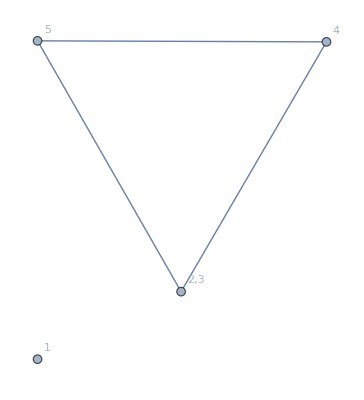

```mathematica
pic[205]
```

```mathematica
EquationsForSol[key_]:=Block[{},
Fold[And,Map[FullSimplify[#]&,
DeleteDuplicates[
Flatten[
With[
{chrom=FullSimplify[sols[key][[1,1]]+sols[key][[1,2]]],
 list1=Table[sols[key][[k,1]],{k,1,5}],
 list2=Table[sols[key][[k,2]],{k,1,5}]
},
With[
{computed=Table[
{
op[key][sols[key][[k,1]]+sols[key][[k,2]],0],
sols[key][[k,1]]>=0,
sols[key][[k,2]]≥0},
{k,1,5}
]
},
Join[{
MakeInEq[chrom,list1,opEqual[key]],
MakeInEq[chrom,list2,opNotEqual[key]]
},computed]
]

]
]
]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.λ->(α+β+γ+δ+ϵ-(α1+β1+γ1+δ1+ϵ1))//Sort
]//DeleteDuplicates//Sort]//FullSimplify//ExpressionToTable
]
```

```mathematica
Table[op[key]=Greater,{key,Keys[sols]}];Table[op[key]=GreaterEqual,{key,Join[{17},Range[100,114],Range[150,154],Range[160,164]]}]
```

{GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual,GreaterEqual}

```mathematica
opEqual=Association[];opNotEqual=Association[]
```

<||>

```mathematica
Table[opEqual[key]=Less,{key,Keys[sols]}];Table[opEqual[key]=LessEqual,{key,Join[{17},Range[100,114],Range[150,154],Range[160,164],Range[205,209]]}]
```

{LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual}

```mathematica
Table[opNotEqual[key]=Less,{key,Keys[sols]}];Table[opNotEqual[key]=LessEqual,{key,Join[{2,4,6,8,10,17},Range[100,114],Range[150,154],Range[160,164],Range[205,209]]}]
```

{LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual,LessEqual}

```mathematica
MyShow3[key_]:=Block[
{matrix=sols[key]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.α+β+γ+δ+ϵ-λ->α1+β1+γ1+δ1+ϵ1},
Labeled[TableForm[Map[Map[TraditionalForm[#]&,#]&,Take[matrix,5]] ,TableAlignments->Center,TableHeadings->{ {1<->3,1<->4,2<->4,2<->5,3<->5,3<->7,4<->7},None}, TableDirections->Column, TableSpacing->{1,0}],Style[TraditionalForm[FullSimplify[matrix[[1,1]]+matrix[[1,2]]]],Red,Bold]]
]
```

```mathematica
TableForm[
Table[
Framed[Row[{Style[key,Darker[Green],Bold],
If[KeyExistsQ[pic,key],Graph[pic[key],GraphLayout->"TutteEmbedding",VertexLabels->"Name", ImageSize->80, VertexLabelStyle->Darker[Darker[Green]]],Null],
MyShow3[key],
Style[EquationsForSol[key],FontSize->9]},"   "]],
{key,Keys[sols]}]
]
```

1-Graphics-1<->3 | α | λ-α
1<->4 | β | λ-β
2<->4 | γ | λ-γ
2<->5 | δ | λ-δ
3<->5 | ϵ | λ-ϵλα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
β+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
      2-Graphics-1<->3 | α | 0
1<->4 | 0 | α
2<->4 | α1 | α-α1
2<->5 | δ1 | α-δ1
3<->5 | 0 | ααα1≥0
δ1≥0
α1+δ1<2 α
α1≤α
δ1≤α
      3-Graphics-1<->3 | 0 | λ-α
1<->4 | β | -α-β+λ
2<->4 | γ-α1 | -α+α1-γ+λ
2<->5 | δ-δ1 | -α-δ+δ1+λ
3<->5 | ϵ | -α+λ-ϵλ-αβ≥0
δ≥δ1
ϵ≥0
β+δ+ϵ≥β1+γ1+δ1+ϵ1
α1+δ1<β+γ+δ+ϵ
3 α1+4 β1+4 γ1+3 δ1+4 ϵ1<3 (β+γ+δ+ϵ)
α1≤γ
α1+β1+γ1+ϵ1≤β+γ+ϵ
α1+β1+γ1+δ1+ϵ1≤β+γ+δ
α1+β1+γ1+δ1+ϵ1≤γ+δ+ϵ
      4-Graphics-1<->3 | 0 | β
1<->4 | β | 0
2<->4 | 0 | β
2<->5 | β1 | β-β1
3<->5 | ϵ1 | β-ϵ1ββ1≥0
ϵ1≥0
β1+ϵ1<2 β
β1≤β
ϵ1≤β
      5-Graphics-1<->3 | α | -α-β+λ
1<->4 | 0 | λ-β
2<->4 | γ | -β-γ+λ
2<->5 | δ-β1 | -β+β1-δ+λ
3<->5 | ϵ-ϵ1 | -β+λ-ϵ+ϵ1λ-βα+γ+δ+ϵ>β1+ϵ1
3 (α+γ+δ+ϵ)>4 α1+3 β1+4 (γ1+δ1)+3 ϵ1
α≥0
γ≥0
α+γ+δ≥α1+β1+γ1+δ1
ϵ≥ϵ1
α+γ+ϵ≥α1+γ1+δ1+ϵ1
α+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
β1≤δ
α1+β1+γ1+δ1+ϵ1≤γ+δ+ϵ
      6-Graphics-1<->3 | α1 | γ-α1
1<->4 | 0 | γ
2<->4 | γ | 0
2<->5 | 0 | γ
3<->5 | γ1 | γ-γ1γα1≥0
γ1≥0
α1+γ1<2 γ
α1≤γ
γ1≤γ
      7-Graphics-1<->3 | α-α1 | -α+α1-γ+λ
1<->4 | β | -β-γ+λ
2<->4 | 0 | λ-γ
2<->5 | δ | -γ-δ+λ
3<->5 | ϵ-γ1 | -γ+γ1+λ-ϵλ-γα+β+δ+ϵ>α1+γ1
3 (α+β+δ+ϵ)>3 α1+4 β1+3 γ1+4 (δ1+ϵ1)
α≥α1
β≥0
δ≥0
α+β+δ≥α1+β1+δ1+ϵ1
α+β+ϵ≥α1+β1+γ1+δ1+ϵ1
α+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
β+δ+ϵ≥β1+γ1+δ1+ϵ1
γ1≤ϵ
      8-Graphics-1<->3 | δ1 | δ-δ1
1<->4 | β1 | δ-β1
2<->4 | 0 | δ
2<->5 | δ | 0
3<->5 | 0 | δδβ1≥0
δ1≥0
β1+δ1<2 δ
β1≤δ
δ1≤δ
      9-Graphics-1<->3 | α-δ1 | -α-δ+δ1+λ
1<->4 | β-β1 | -β+β1-δ+λ
2<->4 | γ | -γ-δ+λ
2<->5 | 0 | λ-δ
3<->5 | ϵ | -δ+λ-ϵλ-δα+β+γ+ϵ>β1+δ1
3 (α+β+γ+ϵ)>4 α1+3 β1+4 γ1+3 δ1+4 ϵ1
α≥δ1
β≥β1
γ≥0
α+β+γ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+ϵ≥α1+γ1+δ1+ϵ1
α1+β1+γ1+ϵ1≤β+γ+ϵ
      10-Graphics-1<->3 | 0 | ϵ
1<->4 | ϵ1 | ϵ-ϵ1
2<->4 | γ1 | ϵ-γ1
2<->5 | 0 | ϵ
3<->5 | ϵ | 0ϵγ1≥0
ϵ1≥0
γ1+ϵ1<2 ϵ
γ1≤ϵ
ϵ1≤ϵ
      11-Graphics-1<->3 | α | -α+λ-ϵ
1<->4 | β-ϵ1 | -β+λ-ϵ+ϵ1
2<->4 | γ-γ1 | -γ+γ1+λ-ϵ
2<->5 | δ | -δ+λ-ϵ
3<->5 | 0 | λ-ϵλ-ϵα+β+γ+δ>γ1+ϵ1
3 (α+β+γ+δ)>4 α1+4 β1+3 γ1+4 δ1+3 ϵ1
α≥0
β≥ϵ1
γ≥γ1
α+β+γ≥α1+β1+γ1+δ1+ϵ1
δ≥0
α+β+δ≥α1+β1+δ1+ϵ1
α+γ+δ≥α1+β1+γ1+δ1
α1+β1+γ1+δ1+ϵ1≤β+γ+δ
      12-Graphics-1<->3 | 0 | -α-β+λ
1<->4 | 0 | -α-β+λ
2<->4 | γ-α1 | -α+α1-β-γ+λ
2<->5 | -β1+δ-δ1 | -α-β+β1-δ+δ1+λ
3<->5 | ϵ-ϵ1 | -α-β+λ-ϵ+ϵ1-α-β+λϵ≥ϵ1
α1+β1+δ1+ϵ1<γ+δ+ϵ
2 α1+2 β1+3 γ1+2 (δ1+ϵ1)<2 (γ+δ+ϵ)
α1≤γ
β1+δ1≤δ
α1+β1+γ1+δ1≤γ+δ
α1+γ1+ϵ1≤γ+ϵ
β1+γ1+δ1+ϵ1≤δ+ϵ
      13-Graphics-1<->3 | α-α1-δ1 | -α+α1-γ-δ+δ1+λ
1<->4 | β-β1 | -β+β1-γ-δ+λ
2<->4 | 0 | -γ-δ+λ
2<->5 | 0 | -γ-δ+λ
3<->5 | ϵ-γ1 | -γ+γ1-δ+λ-ϵ-γ-δ+λα+β+ϵ>α1+β1+γ1+δ1
2 (α+β+ϵ)>2 (α1+β1+γ1+δ1)+3 ϵ1
α≥α1+δ1
β≥β1
α+β≥α1+β1+δ1+ϵ1
α+ϵ≥α1+γ1+δ1+ϵ1
β+ϵ≥β1+γ1+ϵ1
γ1≤ϵ
      14-Graphics-1<->3 | 0 | -α+λ-ϵ
1<->4 | β-ϵ1 | -α-β+λ-ϵ+ϵ1
2<->4 | -α1+γ-γ1 | -α+α1-γ+γ1+λ-ϵ
2<->5 | δ-δ1 | -α-δ+δ1+λ-ϵ
3<->5 | 0 | -α+λ-ϵ-α+λ-ϵβ≥ϵ1
δ≥δ1
β+δ≥β1+δ1+ϵ1
α1+γ1+δ1+ϵ1<β+γ+δ
2 α1+3 β1+2 (γ1+δ1+ϵ1)<2 (β+γ+δ)
α1+γ1≤γ
α1+β1+γ1+δ1≤γ+δ
α1+β1+γ1+ϵ1≤β+γ
      15-Graphics-1<->3 | α-α1 | -α+α1-β-γ+λ
1<->4 | 0 | -β-γ+λ
2<->4 | 0 | -β-γ+λ
2<->5 | δ-β1 | -β+β1-γ-δ+λ
3<->5 | -γ1+ϵ-ϵ1 | -β-γ+γ1+λ-ϵ+ϵ1-β-γ+λα+δ+ϵ>α1+β1+γ1+ϵ1
2 (α+δ+ϵ)>2 α1+2 β1+2 γ1+3 δ1+2 ϵ1
α≥α1
α+δ≥α1+β1+δ1
α+ϵ≥α1+γ1+δ1+ϵ1
β1≤δ
γ1+ϵ1≤ϵ
β1+γ1+δ1+ϵ1≤δ+ϵ
      16-Graphics-1<->3 | α-δ1 | -α-δ+δ1+λ-ϵ
1<->4 | β-β1-ϵ1 | -β+β1-δ+λ-ϵ+ϵ1
2<->4 | γ-γ1 | -γ+γ1-δ+λ-ϵ
2<->5 | 0 | -δ+λ-ϵ
3<->5 | 0 | -δ+λ-ϵ-δ+λ-ϵα+β+γ>β1+γ1+δ1+ϵ1
2 (α+β+γ)>3 α1+2 (β1+γ1+δ1+ϵ1)
α≥δ1
β≥β1+ϵ1
α+β≥α1+β1+δ1+ϵ1
γ≥γ1
α+γ≥α1+γ1+δ1
α1+β1+γ1+ϵ1≤β+γ
      17-Graphics-1<->3 | α1+δ1 | β1+γ1+ϵ1
1<->4 | β1+ϵ1 | α1+γ1+δ1
2<->4 | α1+γ1 | β1+δ1+ϵ1
2<->5 | β1+δ1 | α1+γ1+ϵ1
3<->5 | γ1+ϵ1 | α1+β1+δ1α1+β1+γ1+δ1+ϵ1α1+γ1≥0
α1+δ1≥0
β1+δ1≥0
α1+β1+δ1≥0
α1+γ1+δ1≥0
β1+ϵ1≥0
γ1+ϵ1≥0
α1+γ1+ϵ1≥0
β1+γ1+ϵ1≥0
β1+δ1+ϵ1≥0
      18-Graphics-1<->3 | α1+δ1 | -α1+γ+δ-δ1+ϵ
1<->4 | β1+ϵ1 | -β1+γ+δ+ϵ-ϵ1
2<->4 | γ+γ1 | -γ1+δ+ϵ
2<->5 | δ | γ+ϵ
3<->5 | γ1+ϵ | γ-γ1+δγ+δ+ϵα1+β1+γ+2 γ1+δ+δ1+ϵ+ϵ1>0
γ+γ1≥0
δ≥0
γ+δ≥γ1
α1+δ1≥0
γ+ϵ≥0
γ1+ϵ≥0
δ+ϵ≥γ1
γ+δ+ϵ≥α1+δ1
γ+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α1+β1+γ+2 γ1+δ+δ1+ϵ+ϵ1<5 (γ+δ+ϵ)
      19-Graphics-1<->3 | α | β+ϵ
1<->4 | β+ϵ1 | α+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1+β-γ1+ϵ
2<->5 | β1+δ1 | α+β-β1-δ1+ϵ
3<->5 | ϵ+ϵ1 | α+β-ϵ1α+β+ϵα+α1+β+β1+γ1+δ1+ϵ+2 ϵ1>0
α≥0
α+β≥ϵ1
α1+γ1≥0
β1+δ1≥0
α+ϵ≥ϵ1
β+ϵ≥0
α+β+ϵ≥α1+γ1
α+β+ϵ≥β1+δ1
β+ϵ1≥0
ϵ+ϵ1≥0
α+α1+β+β1+γ1+δ1+ϵ+2 ϵ1<5 (α+β+ϵ)
      20-Graphics-1<->3 | α1+δ1 | -α1+β+γ+δ-δ1
1<->4 | β+β1 | -β1+γ+δ
2<->4 | γ | β+δ
2<->5 | β1+δ | β-β1+γ
3<->5 | γ1+ϵ1 | β+γ-γ1+δ-ϵ1β+γ+δα1+β+2 β1+γ+γ1+δ+δ1+ϵ1>0
β+β1≥0
γ≥0
β+γ≥β1
β+δ≥0
β1+δ≥0
γ+δ≥β1
β+γ+δ≥α1+δ1
β+γ+δ≥γ1+ϵ1
α1+δ1≥0
γ1+ϵ1≥0
α1+β+2 β1+γ+γ1+δ+δ1+ϵ1<5 (β+γ+δ)
      21-Graphics-1<->3 | α+δ1 | δ-δ1+ϵ
1<->4 | β1+ϵ1 | α-β1+δ+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1-γ1+δ+ϵ
2<->5 | δ+δ1 | α-δ1+ϵ
3<->5 | ϵ | α+δα+δ+ϵα+α1+β1+γ1+δ+2 δ1+ϵ+ϵ1>0
α1+γ1≥0
α+δ≥0
α+δ1≥0
δ+δ1≥0
ϵ≥0
α+ϵ≥δ1
δ+ϵ≥δ1
α+δ+ϵ≥α1+γ1
α+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α+α1+β1+γ1+δ+2 δ1+ϵ+ϵ1<5 (α+δ+ϵ)
      22-Graphics-1<->3 | α+α1 | -α1+β+γ
1<->4 | β | α+γ
2<->4 | α1+γ | α-α1+β
2<->5 | β1+δ1 | α+β-β1+γ-δ1
3<->5 | γ1+ϵ1 | α+β+γ-γ1-ϵ1α+β+γα+2 α1+β+β1+γ+γ1+δ1+ϵ1>0
α+α1≥0
β≥0
α+β≥α1
α+γ≥0
α1+γ≥0
β+γ≥α1
α+β+γ≥β1+δ1
α+β+γ≥γ1+ϵ1
β1+δ1≥0
γ1+ϵ1≥0
α+2 α1+β+β1+γ+γ1+δ1+ϵ1<5 (α+β+γ)
      23-Graphics-1<->3 | α | -α+λ+ϵ
1<->4 | β+ϵ1 | -β+λ+ϵ-ϵ1
2<->4 | γ+γ1 | -γ-γ1+λ+ϵ
2<->5 | δ | -δ+λ+ϵ
3<->5 | 2 ϵ | λ-ϵλ+ϵα+β+γ+γ1+δ+2 ϵ+ϵ1>0
α≥0
γ+γ1≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+2 ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+2 ϵ≥α1+β1+2 γ1+δ1+ϵ1
α+γ+δ+2 ϵ≥α1+β1+γ1+δ1+2 ϵ1
β+γ+δ+2 ϵ≥α1+β1+γ1+δ1+ϵ1
β+ϵ1≥0
5 α1+5 β1+6 γ1+5 δ1+6 ϵ1<4 (α+β+γ+δ+2 ϵ)
      24-Graphics-1<->3 | α | -α+β+λ
1<->4 | 2 β | λ-β
2<->4 | γ | β-γ+λ
2<->5 | β1+δ | β-β1-δ+λ
3<->5 | ϵ+ϵ1 | β+λ-ϵ-ϵ1β+λα+2 β+β1+γ+δ+ϵ+ϵ1>0
α≥0
β≥0
γ≥0
β1+δ≥0
α+2 β+γ+δ≥α1+β1+γ1+δ1+2 ϵ1
α+2 β+γ+ϵ≥α1+2 β1+γ1+δ1+ϵ1
α+2 β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
2 β+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
ϵ+ϵ1≥0
5 α1+6 β1+5 (γ1+δ1)+6 ϵ1<4 (α+2 β+γ+δ+ϵ)
      25-Graphics-1<->3 | α+δ1 | -α+δ-δ1+λ
1<->4 | β+β1 | -β-β1+δ+λ
2<->4 | γ | -γ+δ+λ
2<->5 | 2 δ | λ-δ
3<->5 | ϵ | δ+λ-ϵδ+λα+β+β1+γ+2 δ+δ1+ϵ>0
β+β1≥0
γ≥0
δ≥0
α+β+γ+2 δ≥α1+β1+γ1+δ1+ϵ1
α+δ1≥0
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+2 δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+2 δ+ϵ≥α1+2 β1+γ1+δ1+ϵ1
β+γ+2 δ+ϵ≥α1+β1+γ1+2 δ1+ϵ1
5 α1+6 β1+5 γ1+6 δ1+5 ϵ1<4 (α+β+γ+2 δ+ϵ)
      26-Graphics-1<->3 | 2 α | λ-α
1<->4 | β | α-β+λ
2<->4 | α1+γ | α-α1-γ+λ
2<->5 | δ+δ1 | α-δ-δ1+λ
3<->5 | ϵ | α+λ-ϵα+λ2 α+α1+β+γ+δ+δ1+ϵ>0
α≥0
β≥0
α1+γ≥0
2 α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
δ+δ1≥0
ϵ≥0
2 α+β+γ+ϵ≥α1+β1+γ1+2 δ1+ϵ1
2 α+β+δ+ϵ≥2 α1+β1+γ1+δ1+ϵ1
2 α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
β+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
6 α1+5 β1+5 γ1+6 δ1+5 ϵ1<4 (2 α+β+γ+δ+ϵ)
      27-Graphics-1<->3 | α+α1 | -α-α1+γ+λ
1<->4 | β | -β+γ+λ
2<->4 | 2 γ | λ-γ
2<->5 | δ | γ-δ+λ
3<->5 | γ1+ϵ | γ-γ1+λ-ϵγ+λα+α1+β+2 γ+γ1+δ+ϵ>0
α+α1≥0
β≥0
γ≥0
δ≥0
α+β+2 γ+δ≥α1+β1+2 γ1+δ1+ϵ1
α+β+2 γ+ϵ≥α1+β1+γ1+δ1+ϵ1
γ1+ϵ≥0
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+2 γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
β+2 γ+δ+ϵ≥2 α1+β1+γ1+δ1+ϵ1
6 α1+5 β1+6 γ1+5 (δ1+ϵ1)<4 (α+β+2 γ+δ+ϵ)
      281<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ2 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      291<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ2 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      301<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ2 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      311<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ2 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      321<->3 | 2 α | 2 λ-2 α
1<->4 | 2 β | 2 λ-2 β
2<->4 | 2 γ | 2 λ-2 γ
2<->5 | 2 δ | 2 λ-2 δ
3<->5 | 2 ϵ | 2 λ-2 ϵ2 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      331<->3 | 2 α | -2 α+2 λ+ϵ
1<->4 | 2 β+ϵ1 | -2 β+2 λ+ϵ-ϵ1
2<->4 | 2 γ+γ1 | -2 γ-γ1+2 λ+ϵ
2<->5 | 2 δ | -2 δ+2 λ+ϵ
3<->5 | 3 ϵ | 2 λ-2 ϵ2 λ+ϵ2 α+2 β+2 γ+γ1+2 δ+3 ϵ+ϵ1>0
α≥0
2 γ+γ1≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
2 (α+β+γ)+3 ϵ≥2 (α1+β1+γ1+δ1+ϵ1)
2 (α+β+δ)+3 ϵ≥2 α1+2 β1+3 γ1+2 (δ1+ϵ1)
2 (α+γ+δ)+3 ϵ≥2 (α1+β1+γ1+δ1)+3 ϵ1
2 (β+γ+δ)+3 ϵ≥2 (α1+β1+γ1+δ1+ϵ1)
2 β+ϵ1≥0
10 α1+10 β1+11 γ1+10 δ1+11 ϵ1<8 (α+β+γ+δ)+12 ϵ
      341<->3 | 2 α | -2 α+β+2 λ
1<->4 | 3 β | 2 λ-2 β
2<->4 | 2 γ | β-2 γ+2 λ
2<->5 | β1+2 δ | β-β1-2 δ+2 λ
3<->5 | 2 ϵ+ϵ1 | β+2 λ-2 ϵ-ϵ1β+2 λ2 α+3 β+β1+2 (γ+δ+ϵ)+ϵ1>0
α≥0
β≥0
3 β≥2 (α1+β1-γ+γ1-δ+δ1-ϵ+ϵ1)
γ≥0
β1+2 δ≥0
2 α+3 β+2 (γ+δ)≥2 (α1+β1+γ1+δ1)+3 ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
2 α+3 β+2 (γ+ϵ)≥2 α1+3 β1+2 (γ1+δ1+ϵ1)
2 α+3 β+2 (δ+ϵ)≥2 (α1+β1+γ1+δ1+ϵ1)
2 ϵ+ϵ1≥0
10 α1+11 β1+10 (γ1+δ1)+11 ϵ1<8 α+12 β+8 (γ+δ+ϵ)
      351<->3 | 2 α+δ1 | -2 α+δ-δ1+2 λ
1<->4 | 2 β+β1 | -2 β-β1+δ+2 λ
2<->4 | 2 γ | -2 γ+δ+2 λ
2<->5 | 3 δ | 2 λ-2 δ
3<->5 | 2 ϵ | δ+2 λ-2 ϵδ+2 λ2 α+2 β+β1+2 γ+3 δ+δ1+2 ϵ>0
2 β+β1≥0
γ≥0
δ≥0
2 (α+β+γ)+3 δ≥2 (α1+β1+γ1+δ1+ϵ1)
2 α+δ1≥0
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
2 α+2 β+3 δ+2 ϵ≥2 (α1+β1+γ1+δ1+ϵ1)
2 α+2 γ+3 δ+2 ϵ≥2 α1+3 β1+2 (γ1+δ1+ϵ1)
2 β+2 γ+3 δ+2 ϵ≥2 α1+2 β1+2 γ1+3 δ1+2 ϵ1
10 α1+11 β1+10 γ1+11 δ1+10 ϵ1<8 α+8 β+8 γ+12 δ+8 ϵ
      361<->3 | 3 α | 2 λ-2 α
1<->4 | 2 β | α-2 β+2 λ
2<->4 | α1+2 γ | α-α1-2 γ+2 λ
2<->5 | 2 δ+δ1 | α-2 δ-δ1+2 λ
3<->5 | 2 ϵ | α+2 λ-2 ϵα+2 λ3 α+α1+2 β+2 γ+2 δ+δ1+2 ϵ>0
α≥0
3 α≥2 (α1-β+β1-γ+γ1-δ+δ1+ϵ1)
3 α≥2 (α1+β1-γ+γ1-δ+δ1-ϵ+ϵ1)
β≥0
α1+2 γ≥0
2 δ+δ1≥0
ϵ≥0
3 α+2 (β+γ+ϵ)≥2 α1+2 β1+2 γ1+3 δ1+2 ϵ1
3 α+2 (β-β1-γ1+δ-δ1+ϵ-ϵ1)≥3 α1
11 α1+10 β1+10 γ1+11 δ1+10 ϵ1<12 α+8 (β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      371<->3 | 2 α+α1 | -2 α-α1+γ+2 λ
1<->4 | 2 β | -2 β+γ+2 λ
2<->4 | 3 γ | 2 λ-2 γ
2<->5 | 2 δ | γ-2 δ+2 λ
3<->5 | γ1+2 ϵ | γ-γ1+2 λ-2 ϵγ+2 λ2 α+α1+2 β+3 γ+γ1+2 (δ+ϵ)>0
2 α+α1≥0
β≥0
γ≥0
δ≥0
2 α+2 β+3 γ+2 δ≥2 α1+2 β1+3 γ1+2 (δ1+ϵ1)
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
2 α+2 β+3 γ+2 ϵ≥2 (α1+β1+γ1+δ1+ϵ1)
γ1+2 ϵ≥0
2 α+3 γ+2 (δ+ϵ)≥2 (α1+β1+γ1+δ1+ϵ1)
2 β+3 γ+2 (δ+ϵ)≥3 α1+2 (β1+γ1+δ1+ϵ1)
11 α1+10 β1+11 γ1+10 (δ1+ϵ1)<8 α+8 β+12 γ+8 (δ+ϵ)
      381<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ3 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      391<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ3 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      401<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ3 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      411<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ3 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      421<->3 | 3 α | 3 λ-3 α
1<->4 | 3 β | 3 λ-3 β
2<->4 | 3 γ | 3 λ-3 γ
2<->5 | 3 δ | 3 λ-3 δ
3<->5 | 3 ϵ | 3 λ-3 ϵ3 λα+β+γ+δ+ϵ>0
α≥0
β≥0
γ≥0
δ≥0
α+β+γ+δ≥α1+β1+γ1+δ1+ϵ1
ϵ≥0
α+β+γ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+β+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
5 (α1+β1+γ1+δ1+ϵ1)<4 (α+β+γ+δ+ϵ)
α1+β1+γ1+δ1+ϵ1≤β+γ+δ+ϵ
      43-Graphics-1<->3 | α1 | -α1+γ+ϵ
1<->4 | ϵ1 | γ+ϵ-ϵ1
2<->4 | γ+γ1 | ϵ-γ1
2<->5 | 0 | γ+ϵ
3<->5 | γ1+ϵ | γ-γ1γ+ϵα1+γ+2 γ1+ϵ+ϵ1>0
α1≥0
γ≥γ1
γ+γ1≥0
γ+ϵ≥ϵ1
γ1+ϵ≥0
ϵ1≥0
α1+2 γ1+ϵ1<3 (γ+ϵ)
α1≤γ+ϵ
γ1≤ϵ
      44-Graphics-1<->3 | 0 | β+ϵ
1<->4 | β+ϵ1 | ϵ-ϵ1
2<->4 | γ1 | β-γ1+ϵ
2<->5 | β1 | β-β1+ϵ
3<->5 | ϵ+ϵ1 | β-ϵ1β+ϵ3 (β+ϵ)>β1+γ1+2 ϵ1
β+β1+γ1+ϵ+2 ϵ1>0
β≥ϵ1
β1≥0
γ1≥0
ϵ≥ϵ1
β+ϵ≥β1
β+ϵ≥γ1
β+ϵ1≥0
ϵ+ϵ1≥0
      45-Graphics-1<->3 | δ1 | β+δ-δ1
1<->4 | β+β1 | δ-β1
2<->4 | 0 | β+δ
2<->5 | β1+δ | β-β1
3<->5 | ϵ1 | β+δ-ϵ1β+δ3 (β+δ)>2 β1+δ1+ϵ1
β+2 β1+δ+δ1+ϵ1>0
β≥β1
β+β1≥0
β+δ≥δ1
β+δ≥ϵ1
β1+δ≥0
δ1≥0
ϵ1≥0
β1≤δ
      46-Graphics-1<->3 | α+δ1 | δ-δ1
1<->4 | β1 | α-β1+δ
2<->4 | α1 | α-α1+δ
2<->5 | δ+δ1 | α-δ1
3<->5 | 0 | α+δα+δ3 (α+δ)>α1+β1+2 δ1
α+α1+β1+δ+2 δ1>0
α≥δ1
α1≥0
β1≥0
δ≥δ1
α+δ≥α1
α+δ≥β1
α+δ1≥0
δ+δ1≥0
      47-Graphics-1<->3 | α+α1 | γ-α1
1<->4 | 0 | α+γ
2<->4 | α1+γ | α-α1
2<->5 | δ1 | α+γ-δ1
3<->5 | γ1 | α+γ-γ1α+γ3 (α+γ)>2 α1+γ1+δ1
α+2 α1+γ+γ1+δ1>0
α≥α1
α+α1≥0
α+γ≥γ1
α+γ≥δ1
α1+γ≥0
γ1≥0
δ1≥0
α1≤γ
      481<->3 | 2 α | -α+β+λ
1<->4 | 2 β | α-β+λ
2<->4 | α1+γ | α-α1+β-γ+λ
2<->5 | β1+δ+δ1 | α+β-β1-δ-δ1+λ
3<->5 | ϵ+ϵ1 | α+β+λ-ϵ-ϵ1α+β+λ2 α+α1+2 β+β1+γ+δ+δ1+ϵ+ϵ1>0
α≥0
β≥0
α1+γ≥0
2 α+2 β+γ+δ≥α1+β1+γ1+δ1+2 ϵ1
β1+δ+δ1≥0
2 α+2 β+γ+ϵ≥α1+2 β1+γ1+2 δ1+ϵ1
2 α+2 β+δ+ϵ≥2 α1+β1+γ1+δ1+ϵ1
2 α+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
2 β+γ+δ+ϵ≥α1+β1+γ1+δ1+ϵ1
ϵ+ϵ1≥0
6 α1+6 β1+5 γ1+6 (δ1+ϵ1)<4 (2 α+2 β+γ+δ+ϵ)
      491<->3 | α+α1+δ1 | -α-α1+γ+δ-δ1+λ
1<->4 | β+β1 | -β-β1+γ+δ+λ
2<->4 | 2 γ | -γ+δ+λ
2<->5 | 2 δ | γ-δ+λ
3<->5 | γ1+ϵ | γ-γ1+δ+λ-ϵγ+δ+λα+α1+β+β1+2 γ+γ1+2 δ+δ1+ϵ>0
β+β1≥0
γ≥0
δ≥0
α+β+2 (γ+δ)≥α1+β1+2 γ1+δ1+ϵ1
α+α1+δ1≥0
α+β+2 γ+ϵ≥α1+β1+γ1+δ1+ϵ1
γ1+ϵ≥0
α+β+2 δ+ϵ≥α1+β1+γ1+δ1+ϵ1
α+2 (γ+δ)+ϵ≥α1+2 β1+γ1+δ1+ϵ1
β+2 (γ+δ)+ϵ≥2 α1+β1+γ1+2 δ1+ϵ1
6 (α1+β1+γ1+δ1)+5 ϵ1<4 (α+β+2 (γ+δ)+ϵ)
      50-Graphics-1<->3 | 4 (α1+δ1) | 4 (-α1+γ+δ-δ1+ϵ)
1<->4 | 4 (β1+ϵ1) | 4 (-β1+γ+δ+ϵ-ϵ1)
2<->4 | 4 (γ+γ1) | 4 (-γ1+δ+ϵ)
2<->5 | 4 δ | 4 (γ+ϵ)
3<->5 | 4 (γ1+ϵ) | 4 (γ-γ1+δ)4 (γ+δ+ϵ)α1+β1+γ+2 γ1+δ+δ1+ϵ+ϵ1>0
γ+γ1≥0
δ≥0
γ+δ≥γ1
α1+δ1≥0
γ+ϵ≥0
γ1+ϵ≥0
δ+ϵ≥γ1
γ+δ+ϵ≥α1+δ1
γ+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α1+β1+2 γ1+δ1+ϵ1<4 (γ+δ+ϵ)
      51-Graphics-1<->3 | 3 (α1+δ1) | 3 (-α1+γ+δ-δ1+ϵ)
1<->4 | 3 (β1+ϵ1) | 3 (-β1+γ+δ+ϵ-ϵ1)
2<->4 | 3 (γ+γ1) | 3 (-γ1+δ+ϵ)
2<->5 | 3 δ | 3 (γ+ϵ)
3<->5 | 3 (γ1+ϵ) | 3 (γ-γ1+δ)3 (γ+δ+ϵ)α1+β1+γ+2 γ1+δ+δ1+ϵ+ϵ1>0
γ+γ1≥0
δ≥0
γ+δ≥γ1
α1+δ1≥0
γ+ϵ≥0
γ1+ϵ≥0
δ+ϵ≥γ1
γ+δ+ϵ≥α1+δ1
γ+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α1+β1+2 γ1+δ1+ϵ1<4 (γ+δ+ϵ)
      52-Graphics-1<->3 | 2 (α1+δ1) | 2 (-α1+γ+δ-δ1+ϵ)
1<->4 | 2 (β1+ϵ1) | 2 (-β1+γ+δ+ϵ-ϵ1)
2<->4 | 2 (γ+γ1) | 2 (-γ1+δ+ϵ)
2<->5 | 2 δ | 2 (γ+ϵ)
3<->5 | 2 (γ1+ϵ) | 2 (γ-γ1+δ)2 (γ+δ+ϵ)α1+β1+γ+2 γ1+δ+δ1+ϵ+ϵ1>0
γ+γ1≥0
δ≥0
γ+δ≥γ1
α1+δ1≥0
γ+ϵ≥0
γ1+ϵ≥0
δ+ϵ≥γ1
γ+δ+ϵ≥α1+δ1
γ+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α1+β1+2 γ1+δ1+ϵ1<4 (γ+δ+ϵ)
      53-Graphics-1<->3 | α1+δ1 | -α-α1-β+γ+δ-δ1+λ+ϵ
1<->4 | β1+ϵ1 | -α-β-β1+γ+δ+λ+ϵ-ϵ1
2<->4 | -α1+2 γ+γ1 | -α+α1-β-γ-γ1+δ+λ+ϵ
2<->5 | -β1+2 δ-δ1 | -α-β+β1+γ-δ+δ1+λ+ϵ
3<->5 | γ1+2 ϵ-ϵ1 | -α-β+γ-γ1+δ+λ-ϵ+ϵ1-α-β+γ+δ+λ+ϵγ+γ1+δ+ϵ>0
2 γ+γ1≥α1
2 δ≥β1+δ1
2 (γ+δ)≥α1+β1+2 γ1+δ1
α1+δ1≥0
2 (γ+ϵ)≥α1+γ1+ϵ1
2 (δ+ϵ)≥β1+2 γ1+δ1+ϵ1
2 (γ+δ+ϵ)≥2 α1+β1+γ1+2 δ1+ϵ1
2 (γ+δ+ϵ)≥α1+2 β1+γ1+δ1+2 ϵ1
γ1+2 ϵ≥ϵ1
β1+ϵ1≥0
5 α1+5 β1+7 γ1+5 (δ1+ϵ1)<8 (γ+δ+ϵ)
      54-Graphics-1<->3 | δ1 | -α-β+δ-δ1+λ
1<->4 | β1 | -α-β-β1+δ+λ
2<->4 | γ-α1 | -α+α1-β-γ+δ+λ
2<->5 | -β1+2 δ-δ1 | -α-β+β1-δ+δ1+λ
3<->5 | ϵ-ϵ1 | -α-β+δ+λ-ϵ+ϵ1-α-β+δ+λβ1≥0
γ≥α1
2 δ≥β1+δ1
γ+2 δ≥α1+β1+γ1+δ1
δ1≥0
ϵ≥ϵ1
γ+ϵ≥α1+γ1+ϵ1
2 δ+ϵ≥β1+γ1+δ1+ϵ1
γ+2 δ+ϵ≥α1+2 β1+γ1+δ1+ϵ1
γ+2 δ+ϵ≥α1+β1+γ1+2 δ1+ϵ1
α1+ϵ1<γ+2 δ+ϵ
4 α1+5 (β1+γ1+δ1)+4 ϵ1<4 (γ+2 δ+ϵ)
      551<->3 | 4 α | 4 (β+ϵ)
1<->4 | 4 (β+ϵ1) | 4 (α+ϵ-ϵ1)
2<->4 | 4 (α1+γ1) | 4 (α-α1+β-γ1+ϵ)
2<->5 | 4 (β1+δ1) | 4 (α+β-β1-δ1+ϵ)
3<->5 | 4 (ϵ+ϵ1) | 4 (α+β-ϵ1)4 (α+β+ϵ)α+α1+β+β1+γ1+δ1+ϵ+2 ϵ1>0
α≥0
α+β≥ϵ1
α1+γ1≥0
β1+δ1≥0
α+ϵ≥ϵ1
β+ϵ≥0
α+β+ϵ≥α1+γ1
α+β+ϵ≥β1+δ1
β+ϵ1≥0
ϵ+ϵ1≥0
α1+β1+γ1+δ1+2 ϵ1<4 (α+β+ϵ)
      561<->3 | 3 α | 3 (β+ϵ)
1<->4 | 3 (β+ϵ1) | 3 (α+ϵ-ϵ1)
2<->4 | 3 (α1+γ1) | 3 (α-α1+β-γ1+ϵ)
2<->5 | 3 (β1+δ1) | 3 (α+β-β1-δ1+ϵ)
3<->5 | 3 (ϵ+ϵ1) | 3 (α+β-ϵ1)3 (α+β+ϵ)α+α1+β+β1+γ1+δ1+ϵ+2 ϵ1>0
α≥0
α+β≥ϵ1
α1+γ1≥0
β1+δ1≥0
α+ϵ≥ϵ1
β+ϵ≥0
α+β+ϵ≥α1+γ1
α+β+ϵ≥β1+δ1
β+ϵ1≥0
ϵ+ϵ1≥0
α1+β1+γ1+δ1+2 ϵ1<4 (α+β+ϵ)
      571<->3 | 2 α | 2 (β+ϵ)
1<->4 | 2 (β+ϵ1) | 2 (α+ϵ-ϵ1)
2<->4 | 2 (α1+γ1) | 2 (α-α1+β-γ1+ϵ)
2<->5 | 2 (β1+δ1) | 2 (α+β-β1-δ1+ϵ)
3<->5 | 2 (ϵ+ϵ1) | 2 (α+β-ϵ1)2 (α+β+ϵ)α+α1+β+β1+γ1+δ1+ϵ+2 ϵ1>0
α≥0
α+β≥ϵ1
α1+γ1≥0
β1+δ1≥0
α+ϵ≥ϵ1
β+ϵ≥0
α+β+ϵ≥α1+γ1
α+β+ϵ≥β1+δ1
β+ϵ1≥0
ϵ+ϵ1≥0
α1+β1+γ1+δ1+2 ϵ1<4 (α+β+ϵ)
      581<->3 | 2 α-α1-δ1 | -α+α1+β-γ-δ+δ1+λ+ϵ
1<->4 | 2 β-β1+ϵ1 | α-β+β1-γ-δ+λ+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1+β-γ-γ1-δ+λ+ϵ
2<->5 | β1+δ1 | α+β-β1-γ-δ-δ1+λ+ϵ
3<->5 | -γ1+2 ϵ+ϵ1 | α+β-γ+γ1-δ+λ-ϵ-ϵ1α+β-γ-δ+λ+ϵα+β+ϵ+ϵ1>0
2 α≥α1+δ1
2 (α+β)≥α1+β1+δ1+2 ϵ1
α1+γ1≥0
β1+δ1≥0
2 (α+ϵ)≥α1+γ1+δ1+2 ϵ1
2 (β+ϵ)≥β1+γ1+ϵ1
2 (α+β+ϵ)≥2 α1+β1+2 γ1+δ1+ϵ1
2 (α+β+ϵ)≥α1+2 β1+γ1+2 δ1+ϵ1
2 β+ϵ1≥β1
2 ϵ+ϵ1≥γ1
5 (α1+β1+γ1+δ1)+7 ϵ1<8 (α+β+ϵ)
      591<->3 | 2 α-α1-δ1 | -α+α1-γ-δ+δ1+λ
1<->4 | β-β1 | α-β+β1-γ-δ+λ
2<->4 | α1 | α-α1-γ-δ+λ
2<->5 | δ1 | α-γ-δ-δ1+λ
3<->5 | ϵ-γ1 | α-γ+γ1-δ+λ-ϵα-γ-δ+λ2 α≥α1+δ1
α1≥0
β≥β1
2 α+β≥α1+β1+δ1+ϵ1
δ1≥0
ϵ≥γ1
2 α+ϵ≥α1+γ1+δ1+ϵ1
β+ϵ≥β1+γ1+ϵ1
2 α+β+ϵ≥2 α1+β1+γ1+δ1+ϵ1
2 α+β+ϵ≥α1+β1+γ1+2 δ1+ϵ1
β1+γ1<2 α+β+ϵ
5 α1+4 β1+4 γ1+5 (δ1+ϵ1)<4 (2 α+β+ϵ)
      601<->3 | 4 (α1+δ1) | 4 (-α1+β+γ+δ-δ1)
1<->4 | 4 (β+β1) | 4 (-β1+γ+δ)
2<->4 | 4 γ | 4 (β+δ)
2<->5 | 4 (β1+δ) | 4 (β-β1+γ)
3<->5 | 4 (γ1+ϵ1) | 4 (β+γ-γ1+δ-ϵ1)4 (β+γ+δ)α1+β+2 β1+γ+γ1+δ+δ1+ϵ1>0
β+β1≥0
γ≥0
β+γ≥β1
β+δ≥0
β1+δ≥0
γ+δ≥β1
β+γ+δ≥α1+δ1
β+γ+δ≥γ1+ϵ1
α1+δ1≥0
γ1+ϵ1≥0
α1+2 β1+γ1+δ1+ϵ1<4 (β+γ+δ)
      611<->3 | 3 (α1+δ1) | 3 (-α1+β+γ+δ-δ1)
1<->4 | 3 (β+β1) | 3 (-β1+γ+δ)
2<->4 | 3 γ | 3 (β+δ)
2<->5 | 3 (β1+δ) | 3 (β-β1+γ)
3<->5 | 3 (γ1+ϵ1) | 3 (β+γ-γ1+δ-ϵ1)3 (β+γ+δ)α1+β+2 β1+γ+γ1+δ+δ1+ϵ1>0
β+β1≥0
γ≥0
β+γ≥β1
β+δ≥0
β1+δ≥0
γ+δ≥β1
β+γ+δ≥α1+δ1
β+γ+δ≥γ1+ϵ1
α1+δ1≥0
γ1+ϵ1≥0
α1+2 β1+γ1+δ1+ϵ1<4 (β+γ+δ)
      621<->3 | 2 (α1+δ1) | 2 (-α1+β+γ+δ-δ1)
1<->4 | 2 (β+β1) | 2 (-β1+γ+δ)
2<->4 | 2 γ | 2 (β+δ)
2<->5 | 2 (β1+δ) | 2 (β-β1+γ)
3<->5 | 2 (γ1+ϵ1) | 2 (β+γ-γ1+δ-ϵ1)2 (β+γ+δ)α1+β+2 β1+γ+γ1+δ+δ1+ϵ1>0
β+β1≥0
γ≥0
β+γ≥β1
β+δ≥0
β1+δ≥0
γ+δ≥β1
β+γ+δ≥α1+δ1
β+γ+δ≥γ1+ϵ1
α1+δ1≥0
γ1+ϵ1≥0
α1+2 β1+γ1+δ1+ϵ1<4 (β+γ+δ)
      631<->3 | α1+δ1 | -α-α1+β+γ+δ-δ1+λ-ϵ
1<->4 | 2 β+β1-ϵ1 | -α-β-β1+γ+δ+λ-ϵ+ϵ1
2<->4 | -α1+2 γ-γ1 | -α+α1+β-γ+γ1+δ+λ-ϵ
2<->5 | β1+2 δ-δ1 | -α+β-β1+γ-δ+δ1+λ-ϵ
3<->5 | γ1+ϵ1 | -α+β+γ-γ1+δ+λ-ϵ-ϵ1-α+β+γ+δ+λ-ϵβ+β1+γ+δ>0
2 β+β1≥ϵ1
2 γ≥α1+γ1
2 (β+γ)≥α1+2 β1+γ1+ϵ1
2 (β+δ)≥β1+δ1+ϵ1
2 (γ+δ)≥α1+2 β1+γ1+δ1
2 (β+γ+δ)≥2 α1+β1+γ1+2 δ1+ϵ1
2 (β+γ+δ)≥α1+β1+2 γ1+δ1+2 ϵ1
β1+2 δ≥δ1
α1+δ1≥0
γ1+ϵ1≥0
5 α1+7 β1+5 (γ1+δ1+ϵ1)<8 (β+γ+δ)
      641<->3 | α1 | -α-α1+γ+λ-ϵ
1<->4 | β-ϵ1 | -α-β+γ+λ-ϵ+ϵ1
2<->4 | -α1+2 γ-γ1 | -α+α1-γ+γ1+λ-ϵ
2<->5 | δ-δ1 | -α+γ-δ+δ1+λ-ϵ
3<->5 | γ1 | -α+γ-γ1+λ-ϵ-α+γ+λ-ϵα1≥0
β≥ϵ1
2 γ≥α1+γ1
β+2 γ≥α1+β1+γ1+ϵ1
γ1≥0
δ≥δ1
β+δ≥β1+δ1+ϵ1
2 γ+δ≥α1+β1+γ1+δ1
β+2 γ+δ≥2 α1+β1+γ1+δ1+ϵ1
β+2 γ+δ≥α1+β1+2 γ1+δ1+ϵ1
δ1+ϵ1<β+2 γ+δ
5 α1+5 β1+5 γ1+4 (δ1+ϵ1)<4 (β+2 γ+δ)
      651<->3 | 4 (α+δ1) | 4 (δ-δ1+ϵ)
1<->4 | 4 (β1+ϵ1) | 4 (α-β1+δ+ϵ-ϵ1)
2<->4 | 4 (α1+γ1) | 4 (α-α1-γ1+δ+ϵ)
2<->5 | 4 (δ+δ1) | 4 (α-δ1+ϵ)
3<->5 | 4 ϵ | 4 (α+δ)4 (α+δ+ϵ)α+α1+β1+γ1+δ+2 δ1+ϵ+ϵ1>0
α1+γ1≥0
α+δ≥0
α+δ1≥0
δ+δ1≥0
ϵ≥0
α+ϵ≥δ1
δ+ϵ≥δ1
α+δ+ϵ≥α1+γ1
α+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α1+β1+γ1+2 δ1+ϵ1<4 (α+δ+ϵ)
      661<->3 | 3 (α+δ1) | 3 (δ-δ1+ϵ)
1<->4 | 3 (β1+ϵ1) | 3 (α-β1+δ+ϵ-ϵ1)
2<->4 | 3 (α1+γ1) | 3 (α-α1-γ1+δ+ϵ)
2<->5 | 3 (δ+δ1) | 3 (α-δ1+ϵ)
3<->5 | 3 ϵ | 3 (α+δ)3 (α+δ+ϵ)α+α1+β1+γ1+δ+2 δ1+ϵ+ϵ1>0
α1+γ1≥0
α+δ≥0
α+δ1≥0
δ+δ1≥0
ϵ≥0
α+ϵ≥δ1
δ+ϵ≥δ1
α+δ+ϵ≥α1+γ1
α+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α1+β1+γ1+2 δ1+ϵ1<4 (α+δ+ϵ)
      671<->3 | 2 (α+δ1) | 2 (δ-δ1+ϵ)
1<->4 | 2 (β1+ϵ1) | 2 (α-β1+δ+ϵ-ϵ1)
2<->4 | 2 (α1+γ1) | 2 (α-α1-γ1+δ+ϵ)
2<->5 | 2 (δ+δ1) | 2 (α-δ1+ϵ)
3<->5 | 2 ϵ | 2 (α+δ)2 (α+δ+ϵ)α+α1+β1+γ1+δ+2 δ1+ϵ+ϵ1>0
α1+γ1≥0
α+δ≥0
α+δ1≥0
δ+δ1≥0
ϵ≥0
α+ϵ≥δ1
δ+ϵ≥δ1
α+δ+ϵ≥α1+γ1
α+δ+ϵ≥β1+ϵ1
β1+ϵ1≥0
α1+β1+γ1+2 δ1+ϵ1<4 (α+δ+ϵ)
      681<->3 | 2 α-α1+δ1 | -α+α1-β-γ+δ-δ1+λ+ϵ
1<->4 | β1+ϵ1 | α-β-β1-γ+δ+λ+ϵ-ϵ1
2<->4 | α1+γ1 | α-α1-β-γ-γ1+δ+λ+ϵ
2<->5 | -β1+2 δ+δ1 | α-β+β1-γ-δ-δ1+λ+ϵ
3<->5 | -γ1+2 ϵ-ϵ1 | α-β-γ+γ1+δ+λ-ϵ+ϵ1α-β-γ+δ+λ+ϵα+δ+δ1+ϵ>0
α1+γ1≥0
2 (α+δ)≥α1+β1+δ1
2 α+δ1≥α1
2 δ+δ1≥β1
2 ϵ≥γ1+ϵ1
2 (α+ϵ)≥α1+γ1+2 δ1+ϵ1
2 (δ+ϵ)≥β1+γ1+2 δ1+ϵ1
2 (α+δ+ϵ)≥2 α1+β1+2 γ1+δ1+ϵ1
2 (α+δ+ϵ)≥α1+2 β1+γ1+δ1+2 ϵ1
β1+ϵ1≥0
5 α1+5 β1+5 γ1+7 δ1+5 ϵ1<8 (α+δ+ϵ)
      691<->3 | α-α1 | -α+α1-β-γ+λ+ϵ
1<->4 | ϵ1 | -β-γ+λ+ϵ-ϵ1
2<->4 | γ1 | -β-γ-γ1+λ+ϵ
2<->5 | δ-β1 | -β+β1-γ-δ+λ+ϵ
3<->5 | -γ1+2 ϵ-ϵ1 | -β-γ+γ1+λ-ϵ+ϵ1-β-γ+λ+ϵα≥α1
γ1≥0
δ≥β1
α+δ≥α1+β1+δ1
2 ϵ≥γ1+ϵ1
α+2 ϵ≥α1+γ1+δ1+ϵ1
δ+2 ϵ≥β1+γ1+δ1+ϵ1
α+δ+2 ϵ≥α1+β1+2 γ1+δ1+ϵ1
α+δ+2 ϵ≥α1+β1+γ1+δ1+2 ϵ1
ϵ1≥0
α1+β1<α+δ+2 ϵ
4 α1+4 β1+5 (γ1+δ1+ϵ1)<4 (α+δ+2 ϵ)
      701<->3 | 4 (α+α1) | 4 (-α1+β+γ)
1<->4 | 4 β | 4 (α+γ)
2<->4 | 4 (α1+γ) | 4 (α-α1+β)
2<->5 | 4 (β1+δ1) | 4 (α+β-β1+γ-δ1)
3<->5 | 4 (γ1+ϵ1) | 4 (α+β+γ-γ1-ϵ1)4 (α+β+γ)α+2 α1+β+β1+γ+γ1+δ1+ϵ1>0
α+α1≥0
β≥0
α+β≥α1
α+γ≥0
α1+γ≥0
β+γ≥α1
α+β+γ≥β1+δ1
α+β+γ≥γ1+ϵ1
β1+δ1≥0
γ1+ϵ1≥0
2 α1+β1+γ1+δ1+ϵ1<4 (α+β+γ)
      711<->3 | 3 (α+α1) | 3 (-α1+β+γ)
1<->4 | 3 β | 3 (α+γ)
2<->4 | 3 (α1+γ) | 3 (α-α1+β)
2<->5 | 3 (β1+δ1) | 3 (α+β-β1+γ-δ1)
3<->5 | 3 (γ1+ϵ1) | 3 (α+β+γ-γ1-ϵ1)3 (α+β+γ)α+2 α1+β+β1+γ+γ1+δ1+ϵ1>0
α+α1≥0
β≥0
α+β≥α1
α+γ≥0
α1+γ≥0
β+γ≥α1
α+β+γ≥β1+δ1
α+β+γ≥γ1+ϵ1
β1+δ1≥0
γ1+ϵ1≥0
2 α1+β1+γ1+δ1+ϵ1<4 (α+β+γ)
      721<->3 | 2 (α+α1) | 2 (-α1+β+γ)
1<->4 | 2 β | 2 (α+γ)
2<->4 | 2 (α1+γ) | 2 (α-α1+β)
2<->5 | 2 (β1+δ1) | 2 (α+β-β1+γ-δ1)
3<->5 | 2 (γ1+ϵ1) | 2 (α+β+γ-γ1-ϵ1)2 (α+β+γ)α+2 α1+β+β1+γ+γ1+δ1+ϵ1>0
α+α1≥0
β≥0
α+β≥α1
α+γ≥0
α1+γ≥0
β+γ≥α1
α+β+γ≥β1+δ1
α+β+γ≥γ1+ϵ1
β1+δ1≥0
γ1+ϵ1≥0
2 α1+β1+γ1+δ1+ϵ1<4 (α+β+γ)
      731<->3 | 2 α+α1-δ1 | -α-α1+β+γ-δ+δ1+λ-ϵ
1<->4 | 2 β-β1-ϵ1 | α-β+β1+γ-δ+λ-ϵ+ϵ1
2<->4 | α1+2 γ-γ1 | α-α1+β-γ+γ1-δ+λ-ϵ
2<->5 | β1+δ1 | α+β-β1+γ-δ-δ1+λ-ϵ
3<->5 | γ1+ϵ1 | α+β+γ-γ1-δ+λ-ϵ-ϵ1α+β+γ-δ+λ-ϵα+α1+β+γ>0
2 α+α1≥δ1
2 β≥β1+ϵ1
2 (α+β)≥2 α1+β1+δ1+ϵ1
2 (α+γ)≥α1+γ1+δ1
2 (β+γ)≥2 α1+β1+γ1+ϵ1
2 (α+β+γ)≥α1+2 β1+γ1+2 δ1+ϵ1
2 (α+β+γ)≥α1+β1+2 γ1+δ1+2 ϵ1
α1+2 γ≥γ1
β1+δ1≥0
γ1+ϵ1≥0
7 α1+5 (β1+γ1+δ1+ϵ1)<8 (α+β+γ)
      741<->3 | α-δ1 | -α+β-δ+δ1+λ-ϵ
1<->4 | 2 β-β1-ϵ1 | -β+β1-δ+λ-ϵ+ϵ1
2<->4 | γ-γ1 | β-γ+γ1-δ+λ-ϵ
2<->5 | β1 | β-β1-δ+λ-ϵ
3<->5 | ϵ1 | β-δ+λ-ϵ-ϵ1β-δ+λ-ϵα≥δ1
2 β≥β1+ϵ1
α+2 β≥α1+β1+δ1+ϵ1
β1≥0
γ≥γ1
α+γ≥α1+γ1+δ1
2 β+γ≥α1+β1+γ1+ϵ1
α+2 β+γ≥α1+2 β1+γ1+δ1+ϵ1
α+2 β+γ≥α1+β1+γ1+δ1+2 ϵ1
ϵ1≥0
γ1+δ1<α+2 β+γ
5 α1+5 β1+4 (γ1+δ1)+5 ϵ1<4 (α+2 β+γ)
      100-Graphics-1<->3 | α1 | 0
1<->4 | 0 | α1
2<->4 | α1 | 0
2<->5 | 0 | α1
3<->5 | 0 | α1α10
α1
      101-Graphics-1<->3 | 0 | β1
1<->4 | β1 | 0
2<->4 | 0 | β1
2<->5 | β1 | 0
3<->5 | 0 | β1β10
β1
      102-Graphics-1<->3 | 0 | γ1
1<->4 | 0 | γ1
2<->4 | γ1 | 0
2<->5 | 0 | γ1
3<->5 | γ1 | 0γ10
γ1
      103-Graphics-1<->3 | δ1 | 0
1<->4 | 0 | δ1
2<->4 | 0 | δ1
2<->5 | δ1 | 0
3<->5 | 0 | δ1δ10
δ1
      104-Graphics-1<->3 | 0 | ϵ1
1<->4 | ϵ1 | 0
2<->4 | 0 | ϵ1
2<->5 | 0 | ϵ1
3<->5 | ϵ1 | 0ϵ10
ϵ1
      105-Graphics-1<->3 | α-α1 | 0
1<->4 | 0 | α-α1
2<->4 | 0 | α-α1
2<->5 | δ1 | α-α1-δ1
3<->5 | 0 | α-α1α-α1δ1≥0
α1+δ1≤α
      106-Graphics-1<->3 | α-δ1 | 0
1<->4 | 0 | α-δ1
2<->4 | α1 | α-α1-δ1
2<->5 | 0 | α-δ1
3<->5 | 0 | α-δ1α-δ1α1≥0
α1+δ1≤α
      107-Graphics-1<->3 | 0 | β-ϵ1
1<->4 | β-ϵ1 | 0
2<->4 | 0 | β-ϵ1
2<->5 | β1 | β-β1-ϵ1
3<->5 | 0 | β-ϵ1β-ϵ1β1≥0
β1+ϵ1≤β
      108-Graphics-1<->3 | 0 | β-β1
1<->4 | β-β1 | 0
2<->4 | 0 | β-β1
2<->5 | 0 | β-β1
3<->5 | ϵ1 | β-β1-ϵ1β-β1ϵ1≥0
β1+ϵ1≤β
      109-Graphics-1<->3 | 0 | γ-α1
1<->4 | 0 | γ-α1
2<->4 | γ-α1 | 0
2<->5 | 0 | γ-α1
3<->5 | γ1 | -α1+γ-γ1γ-α1γ1≥0
α1+γ1≤γ
      110-Graphics-1<->3 | α1 | -α1+γ-γ1
1<->4 | 0 | γ-γ1
2<->4 | γ-γ1 | 0
2<->5 | 0 | γ-γ1
3<->5 | 0 | γ-γ1γ-γ1α1≥0
α1+γ1≤γ
      111-Graphics-1<->3 | δ1 | -β1+δ-δ1
1<->4 | 0 | δ-β1
2<->4 | 0 | δ-β1
2<->5 | δ-β1 | 0
3<->5 | 0 | δ-β1δ-β1δ1≥0
β1+δ1≤δ
      112-Graphics-1<->3 | 0 | δ-δ1
1<->4 | β1 | -β1+δ-δ1
2<->4 | 0 | δ-δ1
2<->5 | δ-δ1 | 0
3<->5 | 0 | δ-δ1δ-δ1β1≥0
β1+δ1≤δ
      113-Graphics-1<->3 | 0 | ϵ-γ1
1<->4 | ϵ1 | -γ1+ϵ-ϵ1
2<->4 | 0 | ϵ-γ1
2<->5 | 0 | ϵ-γ1
3<->5 | ϵ-γ1 | 0ϵ-γ1ϵ1≥0
γ1+ϵ1≤ϵ
      114-Graphics-1<->3 | 0 | ϵ-ϵ1
1<->4 | 0 | ϵ-ϵ1
2<->4 | γ1 | -γ1+ϵ-ϵ1
2<->5 | 0 | ϵ-ϵ1
3<->5 | ϵ-ϵ1 | 0ϵ-ϵ1γ1≥0
γ1+ϵ1≤ϵ
      140-Graphics-1<->3 | 0 | -α+α1-γ+λ
1<->4 | β | -α+α1-β-γ+λ
2<->4 | 0 | -α+α1-γ+λ
2<->5 | δ-δ1 | -α+α1-γ-δ+δ1+λ
3<->5 | ϵ-γ1 | -α+α1-γ+γ1+λ-ϵ-α+α1-γ+λβ+δ+ϵ>γ1+δ1
β≥0
δ≥δ1
β+δ≥β1+δ1+ϵ1
β+ϵ≥β1+γ1+ϵ1
γ1≤ϵ
β1+γ1+δ1+ϵ1≤δ+ϵ
      141-Graphics-1<->3 | α-α1 | -α+α1-γ+γ1+λ-ϵ
1<->4 | β-ϵ1 | -β-γ+γ1+λ-ϵ+ϵ1
2<->4 | 0 | -γ+γ1+λ-ϵ
2<->5 | δ | -γ+γ1-δ+λ-ϵ
3<->5 | 0 | -γ+γ1+λ-ϵ-γ+γ1+λ-ϵα+β+δ>α1+ϵ1
α≥α1
β≥ϵ1
α+β≥α1+β1+δ1+ϵ1
δ≥0
α+δ≥α1+β1+δ1
β+δ≥β1+δ1+ϵ1
      142-Graphics-1<->3 | α | -α-β+λ-ϵ+ϵ1
1<->4 | 0 | -β+λ-ϵ+ϵ1
2<->4 | γ-γ1 | -β-γ+γ1+λ-ϵ+ϵ1
2<->5 | δ-β1 | -β+β1-δ+λ-ϵ+ϵ1
3<->5 | 0 | -β+λ-ϵ+ϵ1-β+λ-ϵ+ϵ1α+γ+δ>β1+γ1
α≥0
γ≥γ1
α+γ≥α1+γ1+δ1
α+δ≥α1+β1+δ1
β1≤δ
α1+β1+γ1+δ1≤γ+δ
      143-Graphics-1<->3 | α-δ1 | -α-β+β1-δ+δ1+λ
1<->4 | 0 | -β+β1-δ+λ
2<->4 | γ | -β+β1-γ-δ+λ
2<->5 | 0 | -β+β1-δ+λ
3<->5 | ϵ-ϵ1 | -β+β1-δ+λ-ϵ+ϵ1-β+β1-δ+λα+γ+ϵ>δ1+ϵ1
α≥δ1
γ≥0
α+γ≥α1+γ1+δ1
ϵ≥ϵ1
α+ϵ≥α1+γ1+δ1+ϵ1
α1+γ1+ϵ1≤γ+ϵ
      144-Graphics-1<->3 | 0 | -α-δ+δ1+λ
1<->4 | β-β1 | -α-β+β1-δ+δ1+λ
2<->4 | γ-α1 | -α+α1-γ-δ+δ1+λ
2<->5 | 0 | -α-δ+δ1+λ
3<->5 | ϵ | -α-δ+δ1+λ-ϵ-α-δ+δ1+λβ≥β1
ϵ≥0
β+ϵ≥β1+γ1+ϵ1
α1+β1<β+γ+ϵ
α1≤γ
α1+γ1+ϵ1≤γ+ϵ
α1+β1+γ1+ϵ1≤β+γ
      150-Graphics-1<->3 | 0 | -α+α1-β-γ+λ
1<->4 | 0 | -α+α1-β-γ+λ
2<->4 | 0 | -α+α1-β-γ+λ
2<->5 | -β1+δ-δ1 | -α+α1-β+β1-γ-δ+δ1+λ
3<->5 | -γ1+ϵ-ϵ1 | -α+α1-β-γ+γ1+λ-ϵ+ϵ1-α+α1-β-γ+λβ1+δ1≤δ
γ1+ϵ1≤ϵ
      151-Graphics-1<->3 | α-α1-δ1 | -α+α1-γ+γ1-δ+δ1+λ-ϵ
1<->4 | β-β1-ϵ1 | -β+β1-γ+γ1-δ+λ-ϵ+ϵ1
2<->4 | 0 | -γ+γ1-δ+λ-ϵ
2<->5 | 0 | -γ+γ1-δ+λ-ϵ
3<->5 | 0 | -γ+γ1-δ+λ-ϵ-γ+γ1-δ+λ-ϵα≥α1+δ1
β≥β1+ϵ1
      152-Graphics-1<->3 | 0 | -α-β+λ-ϵ+ϵ1
1<->4 | 0 | -α-β+λ-ϵ+ϵ1
2<->4 | -α1+γ-γ1 | -α+α1-β-γ+γ1+λ-ϵ+ϵ1
2<->5 | -β1+δ-δ1 | -α-β+β1-δ+δ1+λ-ϵ+ϵ1
3<->5 | 0 | -α-β+λ-ϵ+ϵ1-α-β+λ-ϵ+ϵ1α1+γ1≤γ
β1+δ1≤δ
      153-Graphics-1<->3 | α-α1-δ1 | -α+α1-β+β1-γ-δ+δ1+λ
1<->4 | 0 | -β+β1-γ-δ+λ
2<->4 | 0 | -β+β1-γ-δ+λ
2<->5 | 0 | -β+β1-γ-δ+λ
3<->5 | -γ1+ϵ-ϵ1 | -β+β1-γ+γ1-δ+λ-ϵ+ϵ1-β+β1-γ-δ+λα≥α1+δ1
γ1+ϵ1≤ϵ
      154-Graphics-1<->3 | 0 | -α-δ+δ1+λ-ϵ
1<->4 | β-β1-ϵ1 | -α-β+β1-δ+δ1+λ-ϵ+ϵ1
2<->4 | -α1+γ-γ1 | -α+α1-γ+γ1-δ+δ1+λ-ϵ
2<->5 | 0 | -α-δ+δ1+λ-ϵ
3<->5 | 0 | -α-δ+δ1+λ-ϵ-α-δ+δ1+λ-ϵβ≥β1+ϵ1
α1+γ1≤γ
      160-Graphics-1<->3 | 0 | -γ1+ϵ-ϵ1
1<->4 | 0 | -γ1+ϵ-ϵ1
2<->4 | 0 | -γ1+ϵ-ϵ1
2<->5 | 0 | -γ1+ϵ-ϵ1
3<->5 | -γ1+ϵ-ϵ1 | 0-γ1+ϵ-ϵ1ϵ
γ1+ϵ1
      161-Graphics-1<->3 | 0 | β-β1-ϵ1
1<->4 | β-β1-ϵ1 | 0
2<->4 | 0 | β-β1-ϵ1
2<->5 | 0 | β-β1-ϵ1
3<->5 | 0 | β-β1-ϵ1β-β1-ϵ1β
β1+ϵ1
      162-Graphics-1<->3 | α-α1-δ1 | 0
1<->4 | 0 | α-α1-δ1
2<->4 | 0 | α-α1-δ1
2<->5 | 0 | α-α1-δ1
3<->5 | 0 | α-α1-δ1α-α1-δ1α
α1+δ1
      163-Graphics-1<->3 | 0 | -α1+γ-γ1
1<->4 | 0 | -α1+γ-γ1
2<->4 | -α1+γ-γ1 | 0
2<->5 | 0 | -α1+γ-γ1
3<->5 | 0 | -α1+γ-γ1-α1+γ-γ1γ
α1+γ1
      164-Graphics-1<->3 | 0 | -β1+δ-δ1
1<->4 | 0 | -β1+δ-δ1
2<->4 | 0 | -β1+δ-δ1
2<->5 | -β1+δ-δ1 | 0
3<->5 | 0 | -β1+δ-δ1-β1+δ-δ1δ
β1+δ1
      200-Graphics-1<->3 | x123 | 0
1<->4 | 0 | x123
2<->4 | 0 | x123
2<->5 | 0 | x123
3<->5 | 0 | x123x1230
x123
      201-Graphics-1<->3 | 0 | x234
1<->4 | 0 | x234
2<->4 | x234 | 0
2<->5 | 0 | x234
3<->5 | 0 | x234x2340
x234
      202-Graphics-1<->3 | 0 | x345
1<->4 | 0 | x345
2<->4 | 0 | x345
2<->5 | 0 | x345
3<->5 | x345 | 0x3450
x345
      203-Graphics-1<->3 | 0 | x451
1<->4 | x451 | 0
2<->4 | 0 | x451
2<->5 | 0 | x451
3<->5 | 0 | x451x4510
x451
      204-Graphics-1<->3 | 0 | x512
1<->4 | 0 | x512
2<->4 | 0 | x512
2<->5 | x512 | 0
3<->5 | 0 | x512x5120
x512
      205-Graphics-1<->3 | α+x123 | 0
1<->4 | 0 | α+x123
2<->4 | α1 | α-α1+x123
2<->5 | δ1 | α-δ1+x123
3<->5 | 0 | α+x123α+x123x123+α>0
α1≥0
δ1≥0
α1≤x123+α
δ1≤x123+α
      206-Graphics-1<->3 | α1 | -α1+γ+x234
1<->4 | 0 | γ+x234
2<->4 | γ+x234 | 0
2<->5 | 0 | γ+x234
3<->5 | γ1 | γ-γ1+x234γ+x234x234+γ>0
α1≥0
γ1≥0
α1≤x234+γ
γ1≤x234+γ
      207-Graphics-1<->3 | 0 | x345+ϵ
1<->4 | ϵ1 | x345+ϵ-ϵ1
2<->4 | γ1 | -γ1+x345+ϵ
2<->5 | 0 | x345+ϵ
3<->5 | x345+ϵ | 0x345+ϵx345+ϵ>0
γ1≥0
ϵ1≥0
γ1≤x345+ϵ
ϵ1≤x345+ϵ
      208-Graphics-1<->3 | 0 | β+x451
1<->4 | β+x451 | 0
2<->4 | 0 | β+x451
2<->5 | β1 | β-β1+x451
3<->5 | ϵ1 | β+x451-ϵ1β+x451x451+β>0
β1≥0
ϵ1≥0
β1≤x451+β
ϵ1≤x451+β
      209-Graphics-1<->3 | δ1 | δ-δ1+x512
1<->4 | β1 | -β1+δ+x512
2<->4 | 0 | δ+x512
2<->5 | δ+x512 | 0
3<->5 | 0 | δ+x512δ+x512x512+δ>0
β1≥0
δ1≥0
β1≤x512+δ
δ1≤x512+δ

```mathematica
opEqual[17]
```

LessEqual

```mathematica
MakeInEq[value_,list_,op_]:=Block[
{i,el,nonzero=0,acc=0},
For[i=1,i≤Length[list],i++,
el=list[[i]];
If[!TrueQ[FullSimplify[el==0]],
If[!TrueQ[FullSimplify[el==value]],
nonzero++;
acc+=el;
]
]
];
If[nonzero==0,
True,
op[acc,value*nonzero]
]
]
```

```mathematica
ExpressionToTable[exp_]:=Block[
{vals=Sort[Table[exp[[i]]//FullSimplify,{i,1,Length[exp]}]]},
(*Print[vals];*)
TableForm[Table[vals[[i]],{i,1,Length[vals]}]//Sort,TableDirections->Column]
]
```

```mathematica
Fold[And,Map[FullSimplify[#]&,
DeleteDuplicates[
Flatten[
Table[
With[
{chrom=FullSimplify[sols[key][[1,1]]+sols[key][[1,2]]],
 list1=Table[sols[key][[k,1]],{k,1,5}],
 list2=Table[sols[key][[k,2]],{k,1,5}]
},
With[
{computed=Table[
{
op[key][sols[key][[k,1]]+sols[key][[k,2]],0],
sols[key][[k,1]]>=0,
sols[key][[k,2]]≥0},
{k,1,5}
]
},
Join[{
PrintTemporary[{chrom,opEqual[key]//TraditionalForm,list1}];
MakeInEq[chrom,list1,opEqual[key]],
PrintTemporary[{chrom,opNotEqual[key]//TraditionalForm,list2}];
MakeInEq[chrom,list2,opNotEqual[key]]
},computed]
]

],{key,Keys[sols]}
]
]
]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.λ->(α+β+γ+δ+ϵ-(α1+β1+γ1+δ1+ϵ1))//Sort
]//DeleteDuplicates//Sort]//FullSimplify//ExpressionToTable
```

x123>0
x234>0
x345>0
x451>0
x512>0
α>0
β>0
γ>0
δ>0
ϵ>0
α1≥0
β1≥0
γ1≥0
δ1≥0
ϵ1≥0
2 α1+2 β1+2 γ1+3 δ1+2 ϵ1<2 (α+δ+ϵ)
2 (α1+β1+γ1+δ1)+3 ϵ1<2 (α+β+ϵ)
2 α1+2 β1+3 γ1+2 (δ1+ϵ1)<2 (γ+δ+ϵ)
2 α1+3 β1+2 (γ1+δ1+ϵ1)<2 (β+γ+δ)
3 α1+2 (β1+γ1+δ1+ϵ1)<2 (α+β+γ)
α1+γ1≤γ
α1+δ1≤α
β1+δ1≤δ
β1+ϵ1≤β
γ1+ϵ1≤ϵ

```mathematica
(*||α+β>α1+β1+δ1+ϵ1||γ+δ>α1+β1+γ1+δ1||α+ϵ>α1+γ1+δ1+ϵ1||β+γ>α1+β1+γ1+ϵ1*)
```

```mathematica
{α>0,β>0,γ>0,δ>0,ϵ>0,α1≥0,β1≥0,γ1≥0,δ1≥0,ϵ1≥0,2 α1+2 β1+2 γ1+3 δ1+2 ϵ1<2 (α+δ+ϵ),2 (α1+β1+γ1+δ1)+3 ϵ1<2 (α+β+ϵ),2 α1+2 β1+3 γ1+2 (δ1+ϵ1)<2 (γ+δ+ϵ),2 α1+3 β1+2 (γ1+δ1+ϵ1)<2 (β+γ+δ),3 α1+2 (β1+γ1+δ1+ϵ1)<2 (α+β+γ),α1+γ1≤γ,α1+δ1≤α,β1+δ1≤δ,β1+ϵ1≤β,γ1+ϵ1≤ϵ}//Length
```

20

```mathematica
Fold[And,Map[FullSimplify[#]&,DeleteDuplicates[Flatten[Table[Table[{op[key][sols[key][[k,1]]+sols[key][[k,2]],0],sols[key][[k,1]]>=0,sols[key][[k,2]]≥0},{k,1,5}],{key,Keys[sols]}]]]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1}/.λ->(α+β+γ+δ+ϵ-(α1+β1+γ1+δ1+ϵ1))//Sort
]//DeleteDuplicates//Sort]&&γ-γ1>0&&ϵ-ϵ1>0&&-β1+2 δ-δ1>0//FullSimplify//ExpressionToTable
```

x123>0
x234>0
x345>0
x451>0
x512>0
α>0
β>0
δ>0
α1≥0
β1≥0
γ1≥0
δ1≥0
ϵ1≥0
γ1<γ
ϵ1<ϵ
α1+β1+γ1+δ1+ϵ1<β+γ+δ
α1+β1+γ1+δ1+ϵ1<α+β+ϵ
α1+β1+γ1+δ1+ϵ1<α+δ+ϵ
α1+γ1≤γ
α1+δ1≤α
β1+δ1≤δ
β1+ϵ1≤β
γ1+ϵ1≤ϵ

```mathematica
Fold[And,Map[FullSimplify[#]&,DeleteDuplicates[Flatten[Table[Table[{op[key][sols[key][[k,1]]+sols[key][[k,2]],0],sols[key][[k,1]]>=0,sols[key][[k,2]]≥0},{k,1,5}]/.{α2->δ1,β2->ϵ1,γ2->α1,δ2->β1,ϵ2->γ1},{key,Keys[sols]}]]]//Sort
]//DeleteDuplicates//Sort]//FullSimplify//ExpressionToTable
```

x123>0
x234>0
x345>0
x451>0
x512>0
α>0
β>0
γ>0
δ>0
ϵ>0
α1≥0
β1≥0
γ1≥0
δ1≥0
ϵ1≥0
α+β<λ
β+γ<λ
γ+δ<λ
α+ϵ<λ
δ+ϵ<λ
α1+γ1≤γ
α+β+γ+δ≤α1+β1+δ1+λ
α1+δ1≤α
β1+δ1≤δ
α+β+γ+ϵ≤α1+γ1+ϵ1+λ
α+β+δ+ϵ≤β1+δ1+ϵ1+λ
α+γ+δ+ϵ≤α1+γ1+δ1+λ
β+γ+δ+ϵ≤β1+γ1+ϵ1+λ
β1+ϵ1≤β
γ1+ϵ1≤ϵ
α1+γ1+λ≤α+β+γ+δ+ϵ
α1+δ1+λ≤α+β+γ+δ+ϵ
β1+δ1+λ≤α+β+γ+δ+ϵ
β1+ϵ1+λ≤α+β+γ+δ+ϵ
γ1+ϵ1+λ≤α+β+γ+δ+ϵ